# 2-target 2-allele model with independent recombination and mutations

## Introduction

In the following, we consider a model with one PRDM9-like locus A and two targets B and C. We assume that B and C loci have two alleles, B1 and B2 and C1 and C2. A locus has 4 alleles. A11 and A12 attempts to bind locus B with probability P1, and C with probability 1 - P1. A21 and A22 attempts to bind locus B with probability P2, and C with probability 1 - P2. A11 and A21 match with alleles B1 and C1, while A12 and A22 match with alleles B2 and C2. Note that by considering that P1 = P2 = 1/2, alleles A11 and A21 are really the same, as are alleles A12 and A22. So, by assuming P1 = P2 = 1/2, we are considering only two alleles on A that attempts to bind loci B and C indistinctly, which is the case explored in the paper. Here, the model is exposed for any value of P1 and P2, but the numerical computations and the figures are done only for P1 = P2 = 1/2.

## Recursion

### Random Mating

There are 16 possible haplotypes: A11 B1 C1, A11 B1 C2, A11 B2 C1, A11 B2 C2, A12 B1 C1, A12 B1 C2, A12 B2 C1, A12 B2 C2, A21 B1 C1, A21 B1 C2, A21 B2 C1, A21 B2 C2, A22 B1 C1, A22 B1 C2, A22 B2 C1, and A22 B2 C2. Their frequencies are noted x1111, x1112, x1121, x1122, x1211, x1212, x1221, x1222, x2111, x2112, x2121, x2122, x2211, x2212, x2221 and x2222.

We note Haplotypes the 4-dimension array compiling all 16 haplotype frequencies

```mathematica
Haplotypes={{{{x1111,x1112},{x1121,x1122}},{{x1211,x1212},{x1221,x1222}}},{{{x2111,x2112},{x2121,x2122}},{{x2211,x2212},{x2221,x2222}}}};
```

We note Genotypes the 8-dimension array compiling all 16 x 16 =  256 possible ordered genotype frequencies. Genotypes are noted similarly to haplotypes : x11221121 is the frequency of genotype A11 B2 C2 / A11 B2 C1 for example. Genotypes are ordered: frequencies of genotypes A12 B1 C1 / A22 B2 C1 and A22 B2 C1 / A12 B1 C1 are noted in different cells of the array.

```mathematica
Genotypes={{{{{{{{x11111111,x11111112},{x11111121,x11111122}},{{x11111211,x11111212},{x11111221,x11111222}}},{{{x11112111,x11112112},{x11112121,x11112122}},{{x11112211,x11112211},{x11112221,x11112222}}}},{{{{x11121111,x11121112},{x11121121,x11121122}},{{x11121211,x11121212},{x11121221,x11121222}}},{{{x11122111,x11122112},{x11122121,x11122122}},{{x11122211,x11122211},{x11122221,x11122222}}}}},{{{{{x11211111,x11211112},{x11211121,x11211122}},{{x11211211,x11211212},{x11211221,x11211222}}},{{{x11212111,x11212112},{x11212121,x11212122}},{{x11212211,x11212211},{x11212221,x11212222}}}},{{{{x11221111,x11221112},{x11221121,x11221122}},{{x11221211,x11221212},{x11221221,x11221222}}},{{{x11222111,x11222112},{x11222121,x11222122}},{{x11222211,x11222211},{x11222221,x11222222}}}}}},{{{{{{x12111111,x12111112},{x12111121,x12111122}},{{x12111211,x12111212},{x12111221,x12111222}}},{{{x12112111,x12112112},{x12112121,x12112122}},{{x12112211,x12112211},{x12112221,x12112222}}}},{{{{x12121111,x12121112},{x12121121,x12121122}},{{x12121211,x12121212},{x12121221,x12121222}}},{{{x12122111,x12122112},{x12122121,x12122122}},{{x12122211,x12122211},{x12122221,x12122222}}}}},{{{{{x12211111,x12211112},{x12211121,x12211122}},{{x12211211,x12211212},{x12211221,x12211222}}},{{{x12212111,x12212112},{x12212121,x12212122}},{{x12212211,x12212211},{x12212221,x12212222}}}},{{{{x12221111,x12221112},{x12221121,x12221122}},{{x12221211,x12221212},{x12221221,x12221222}}},{{{x12222111,x12222112},{x12222121,x12222122}},{{x12222211,x12222211},{x12222221,x12222222}}}}}}},{{{{{{{x21111111,x21111112},{x21111121,x21111122}},{{x21111211,x21111212},{x21111221,x21111222}}},{{{x21112111,x21112112},{x21112121,x21112122}},{{x21112211,x21112211},{x21112221,x21112222}}}},{{{{x21121111,x21121112},{x21121121,x21121122}},{{x21121211,x21121212},{x21121221,x21121222}}},{{{x21122111,x21122112},{x21122121,x21122122}},{{x21122211,x21122211},{x21122221,x21122222}}}}},{{{{{x21211111,x21211112},{x21211121,x21211122}},{{x21211211,x21211212},{x21211221,x21211222}}},{{{x21212111,x21212112},{x21212121,x21212122}},{{x21212211,x21212211},{x21212221,x21212222}}}},{{{{x21221111,x21221112},{x21221121,x21221122}},{{x21221211,x21221212},{x21221221,x21221222}}},{{{x21222111,x21222112},{x21222121,x21222122}},{{x21222211,x21222211},{x21222221,x21222222}}}}}},{{{{{{x22111111,x22111112},{x22111121,x22111122}},{{x22111211,x22111212},{x22111221,x22111222}}},{{{x22112111,x22112112},{x22112121,x22112122}},{{x22112211,x22112211},{x22112221,x22112222}}}},{{{{x22121111,x22121112},{x22121121,x22121122}},{{x22121211,x22121212},{x22121221,x22121222}}},{{{x22122111,x22122112},{x22122121,x22122122}},{{x22122211,x22122211},{x22122221,x22122222}}}}},{{{{{x22211111,x22211112},{x22211121,x22211122}},{{x22211211,x22211212},{x22211221,x22211222}}},{{{x22212111,x22212112},{x22212121,x22212122}},{{x22212211,x22212211},{x22212221,x22212222}}}},{{{{x22221111,x22221112},{x22221121,x22221122}},{{x22221211,x22221212},{x22221221,x22221222}}},{{{x22222111,x22222112},{x22222121,x22222122}},{{x22222211,x22222211},{x22222221,x22222222}}}}}}}};
```

We assume random mating between individuals, such that Genotypes[i,j,k,l,m,n,o,p] = Haplotypes[i,k,m,o] * Haplotypes[j,l,n,p] (for any value of i,j,k,m,n,o since genotypes are ordered).

```mathematica
For[i=1,i<3,++i,
For[j=1,j<3,++j,
For[k=1,k<3,++k,
For[l=1,l<3,++l,
For[m=1,m<3,++m,
For[n=1,n<3,++n,
For[o=1,o<3,++o,
For[p=1,p<3,++p,
Genotypes[[i,j,k,l,m,n,o,p]]=Haplotypes[[i,k,m,o]]*Haplotypes[[j,l,n,p]]]]]]]]]];
```

### Recombination

GenotypesR is the 8-dimension array compiling frequencies of genotypes after recombination. We first create the array by filling it up with zeros.

```mathematica
GenotypesR=Table[0,{i,1,2},{j,1,2},{k,1,2},{l,1,2},{m,1,2},{n,1,2},{o,1,2},{p,1,2}];
```

We note rAB the recombination rate between loci A an B and rBC the recombination rate between loci B and C. We do not consider that crossing-over and recombination between loci depends on binding between A alleles and target: rAB and rBC are fixed parameter of the model, that do not depend on the genotype considered.

Genotype Aik Bm Co / Ajl Bn Cp can be produced from: genotype Aik Bm Co / Ajl Bn Cp (no recombination at all, with probability (1 - rAB) (1 - rBC)) ; Aik Bn Cp / Ajl Bm Co (recombination between A and B only, with probability rAB (1 - rBC)) ; Aik Bm Cp / Ajl Bn Co (recombination between B and C only, with probability rBC (1 - rAB)) ; Aik Bn Co / Ajl Bm Cp (recombination between A and B and between B and C, with probability rAB rBC).

```mathematica
For[i=1,i<3,++i,
For[j=1,j<3,++j,
For[k=1,k<3,++k,
For[l=1,l<3,++l,
For[m=1,m<3,++m,
For[n=1,n<3,++n,
For[o=1,o<3,++o,
For[p=1,p<3,++p,
GenotypesR[[i,j,k,l,m,n,o,p]]=(1-rAB)(1-rBC)Genotypes[[i,j,k,l,m,n,o,p]]+rAB(1-rBC)Genotypes[[i,j,k,l,n,m,p,o]]+rBC(1-rAB)Genotypes[[i,j,k,l,m,n,p,o]]+rAB rBC Genotypes[[i,j,k,l,n,m,o,p]]//FullSimplify]]]]]]]];
```

We create a function that returns the 8-dimension array of genotype frequencies after recombination, and that take as argument the 4-dimension array of haplotype frequencies at previous generation and recombination rates rAB and rBC. This function compiles the effect of both random mating and recombination.

```mathematica
GenR[{rAB_,rBC_},{{{{x1111_,x1112_},{x1121_,x1122_}},{{x1211_,x1212_},{x1221_,x1222_}}},{{{x2111_,x2112_},{x2121_,x2122_}},{{x2211_,x2212_},{x2221_,x2222_}}}}]:={{{{{{{{GenotypesR[[1,1,1,1,1,1,1,1]],GenotypesR[[1,1,1,1,1,1,1,2]]},{GenotypesR[[1,1,1,1,1,1,2,1]],GenotypesR[[1,1,1,1,1,1,2,2]]}},{{GenotypesR[[1,1,1,1,1,2,1,1]],GenotypesR[[1,1,1,1,1,2,1,2]]},{GenotypesR[[1,1,1,1,1,2,2,1]],GenotypesR[[1,1,1,1,1,2,2,2]]}}},{{{GenotypesR[[1,1,1,1,2,1,1,1]],GenotypesR[[1,1,1,1,2,1,1,2]]},{GenotypesR[[1,1,1,1,2,1,2,1]],GenotypesR[[1,1,1,1,2,1,2,2]]}},{{GenotypesR[[1,1,1,1,2,2,1,1]],GenotypesR[[1,1,1,1,2,2,1,2]]},{GenotypesR[[1,1,1,1,2,2,2,1]],GenotypesR[[1,1,1,1,2,2,2,2]]}}}},{{{{GenotypesR[[1,1,1,2,1,1,1,1]],GenotypesR[[1,1,1,2,1,1,1,2]]},{GenotypesR[[1,1,1,2,1,1,2,1]],GenotypesR[[1,1,1,2,1,1,2,2]]}},{{GenotypesR[[1,1,1,2,1,2,1,1]],GenotypesR[[1,1,1,2,1,2,1,2]]},{GenotypesR[[1,1,1,2,1,2,2,1]],GenotypesR[[1,1,1,2,1,2,2,2]]}}},{{{GenotypesR[[1,1,1,2,2,1,1,1]],GenotypesR[[1,1,1,2,2,1,1,2]]},{GenotypesR[[1,1,1,2,2,1,2,1]],GenotypesR[[1,1,1,2,2,1,2,2]]}},{{GenotypesR[[1,1,1,2,2,2,1,1]],GenotypesR[[1,1,1,2,2,2,1,2]]},{GenotypesR[[1,1,1,2,2,2,2,1]],GenotypesR[[1,1,1,2,2,2,2,2]]}}}}},{{{{{GenotypesR[[1,1,2,1,1,1,1,1]],GenotypesR[[1,1,2,1,1,1,1,2]]},{GenotypesR[[1,1,2,1,1,1,2,1]],GenotypesR[[1,1,2,1,1,1,2,2]]}},{{GenotypesR[[1,1,2,1,1,2,1,1]],GenotypesR[[1,1,2,1,1,2,1,2]]},{GenotypesR[[1,1,2,1,1,2,2,1]],GenotypesR[[1,1,2,1,1,2,2,2]]}}},{{{GenotypesR[[1,1,2,1,2,1,1,1]],GenotypesR[[1,1,2,1,2,1,1,2]]},{GenotypesR[[1,1,2,1,2,1,2,1]],GenotypesR[[1,1,2,1,2,1,2,2]]}},{{GenotypesR[[1,1,2,1,2,2,1,1]],GenotypesR[[1,1,2,1,2,2,1,2]]},{GenotypesR[[1,1,2,1,2,2,2,1]],GenotypesR[[1,1,2,1,2,2,2,2]]}}}},{{{{GenotypesR[[1,1,2,2,1,1,1,1]],GenotypesR[[1,1,2,2,1,1,1,2]]},{GenotypesR[[1,1,2,2,1,1,2,1]],GenotypesR[[1,1,2,2,1,1,2,2]]}},{{GenotypesR[[1,1,2,2,1,2,1,1]],GenotypesR[[1,1,2,2,1,2,1,2]]},{GenotypesR[[1,1,2,2,1,2,2,1]],GenotypesR[[1,1,2,2,1,2,2,2]]}}},{{{GenotypesR[[1,1,2,2,2,1,1,1]],GenotypesR[[1,1,2,2,2,1,1,2]]},{GenotypesR[[1,1,2,2,2,1,2,1]],GenotypesR[[1,1,2,2,2,1,2,2]]}},{{GenotypesR[[1,1,2,2,2,2,1,1]],GenotypesR[[1,1,2,2,2,2,1,2]]},{GenotypesR[[1,1,2,2,2,2,2,1]],GenotypesR[[1,1,2,2,2,2,2,2]]}}}}}},{{{{{{GenotypesR[[1,2,1,1,1,1,1,1]],GenotypesR[[1,2,1,1,1,1,1,2]]},{GenotypesR[[1,2,1,1,1,1,2,1]],GenotypesR[[1,2,1,1,1,1,2,2]]}},{{GenotypesR[[1,2,1,1,1,2,1,1]],GenotypesR[[1,2,1,1,1,2,1,2]]},{GenotypesR[[1,2,1,1,1,2,2,1]],GenotypesR[[1,2,1,1,1,2,2,2]]}}},{{{GenotypesR[[1,2,1,1,2,1,1,1]],GenotypesR[[1,2,1,1,2,1,1,2]]},{GenotypesR[[1,2,1,1,2,1,2,1]],GenotypesR[[1,2,1,1,2,1,2,2]]}},{{GenotypesR[[1,2,1,1,2,2,1,1]],GenotypesR[[1,2,1,1,2,2,1,2]]},{GenotypesR[[1,2,1,1,2,2,2,1]],GenotypesR[[1,2,1,1,2,2,2,2]]}}}},{{{{GenotypesR[[1,2,1,2,1,1,1,1]],GenotypesR[[1,2,1,2,1,1,1,2]]},{GenotypesR[[1,2,1,2,1,1,2,1]],GenotypesR[[1,2,1,2,1,1,2,2]]}},{{GenotypesR[[1,2,1,2,1,2,1,1]],GenotypesR[[1,2,1,2,1,2,1,2]]},{GenotypesR[[1,2,1,2,1,2,2,1]],GenotypesR[[1,2,1,2,1,2,2,2]]}}},{{{GenotypesR[[1,2,1,2,2,1,1,1]],GenotypesR[[1,2,1,2,2,1,1,2]]},{GenotypesR[[1,2,1,2,2,1,2,1]],GenotypesR[[1,2,1,2,2,1,2,2]]}},{{GenotypesR[[1,2,1,2,2,2,1,1]],GenotypesR[[1,2,1,2,2,2,1,2]]},{GenotypesR[[1,2,1,2,2,2,2,1]],GenotypesR[[1,2,1,2,2,2,2,2]]}}}}},{{{{{GenotypesR[[1,2,2,1,1,1,1,1]],GenotypesR[[1,2,2,1,1,1,1,2]]},{GenotypesR[[1,2,2,1,1,1,2,1]],GenotypesR[[1,2,2,1,1,1,2,2]]}},{{GenotypesR[[1,2,2,1,1,2,1,1]],GenotypesR[[1,2,2,1,1,2,1,2]]},{GenotypesR[[1,2,2,1,1,2,2,1]],GenotypesR[[1,2,2,1,1,2,2,2]]}}},{{{GenotypesR[[1,2,2,1,2,1,1,1]],GenotypesR[[1,2,2,1,2,1,1,2]]},{GenotypesR[[1,2,2,1,2,1,2,1]],GenotypesR[[1,2,2,1,2,1,2,2]]}},{{GenotypesR[[1,2,2,1,2,2,1,1]],GenotypesR[[1,2,2,1,2,2,1,2]]},{GenotypesR[[1,2,2,1,2,2,2,1]],GenotypesR[[1,2,2,1,2,2,2,2]]}}}},{{{{GenotypesR[[1,2,2,2,1,1,1,1]],GenotypesR[[1,2,2,2,1,1,1,2]]},{GenotypesR[[1,2,2,2,1,1,2,1]],GenotypesR[[1,2,2,2,1,1,2,2]]}},{{GenotypesR[[1,2,2,2,1,2,1,1]],GenotypesR[[1,2,2,2,1,2,1,2]]},{GenotypesR[[1,2,2,2,1,2,2,1]],GenotypesR[[1,2,2,2,1,2,2,2]]}}},{{{GenotypesR[[1,2,2,2,2,1,1,1]],GenotypesR[[1,2,2,2,2,1,1,2]]},{GenotypesR[[1,2,2,2,2,1,2,1]],GenotypesR[[1,2,2,2,2,1,2,2]]}},{{GenotypesR[[1,2,2,2,2,2,1,1]],GenotypesR[[1,2,2,2,2,2,1,2]]},{GenotypesR[[1,2,2,2,2,2,2,1]],GenotypesR[[1,2,2,2,2,2,2,2]]}}}}}}},{{{{{{{GenotypesR[[2,1,1,1,1,1,1,1]],GenotypesR[[2,1,1,1,1,1,1,2]]},{GenotypesR[[2,1,1,1,1,1,2,1]],GenotypesR[[2,1,1,1,1,1,2,2]]}},{{GenotypesR[[2,1,1,1,1,2,1,1]],GenotypesR[[2,1,1,1,1,2,1,2]]},{GenotypesR[[2,1,1,1,1,2,2,1]],GenotypesR[[2,1,1,1,1,2,2,2]]}}},{{{GenotypesR[[2,1,1,1,2,1,1,1]],GenotypesR[[2,1,1,1,2,1,1,2]]},{GenotypesR[[2,1,1,1,2,1,2,1]],GenotypesR[[2,1,1,1,2,1,2,2]]}},{{GenotypesR[[2,1,1,1,2,2,1,1]],GenotypesR[[2,1,1,1,2,2,1,2]]},{GenotypesR[[2,1,1,1,2,2,2,1]],GenotypesR[[2,1,1,1,2,2,2,2]]}}}},{{{{GenotypesR[[2,1,1,2,1,1,1,1]],GenotypesR[[2,1,1,2,1,1,1,2]]},{GenotypesR[[2,1,1,2,1,1,2,1]],GenotypesR[[2,1,1,2,1,1,2,2]]}},{{GenotypesR[[2,1,1,2,1,2,1,1]],GenotypesR[[2,1,1,2,1,2,1,2]]},{GenotypesR[[2,1,1,2,1,2,2,1]],GenotypesR[[2,1,1,2,1,2,2,2]]}}},{{{GenotypesR[[2,1,1,2,2,1,1,1]],GenotypesR[[2,1,1,2,2,1,1,2]]},{GenotypesR[[2,1,1,2,2,1,2,1]],GenotypesR[[2,1,1,2,2,1,2,2]]}},{{GenotypesR[[2,1,1,2,2,2,1,1]],GenotypesR[[2,1,1,2,2,2,1,2]]},{GenotypesR[[2,1,1,2,2,2,2,1]],GenotypesR[[2,1,1,2,2,2,2,2]]}}}}},{{{{{GenotypesR[[2,1,2,1,1,1,1,1]],GenotypesR[[2,1,2,1,1,1,1,2]]},{GenotypesR[[2,1,2,1,1,1,2,1]],GenotypesR[[2,1,2,1,1,1,2,2]]}},{{GenotypesR[[2,1,2,1,1,2,1,1]],GenotypesR[[2,1,2,1,1,2,1,2]]},{GenotypesR[[2,1,2,1,1,2,2,1]],GenotypesR[[2,1,2,1,1,2,2,2]]}}},{{{GenotypesR[[2,1,2,1,2,1,1,1]],GenotypesR[[2,1,2,1,2,1,1,2]]},{GenotypesR[[2,1,2,1,2,1,2,1]],GenotypesR[[2,1,2,1,2,1,2,2]]}},{{GenotypesR[[2,1,2,1,2,2,1,1]],GenotypesR[[2,1,2,1,2,2,1,2]]},{GenotypesR[[2,1,2,1,2,2,2,1]],GenotypesR[[2,1,2,1,2,2,2,2]]}}}},{{{{GenotypesR[[2,1,2,2,1,1,1,1]],GenotypesR[[2,1,2,2,1,1,1,2]]},{GenotypesR[[2,1,2,2,1,1,2,1]],GenotypesR[[2,1,2,2,1,1,2,2]]}},{{GenotypesR[[2,1,2,2,1,2,1,1]],GenotypesR[[2,1,2,2,1,2,1,2]]},{GenotypesR[[2,1,2,2,1,2,2,1]],GenotypesR[[2,1,2,2,1,2,2,2]]}}},{{{GenotypesR[[2,1,2,2,2,1,1,1]],GenotypesR[[2,1,2,2,2,1,1,2]]},{GenotypesR[[2,1,2,2,2,1,2,1]],GenotypesR[[2,1,2,2,2,1,2,2]]}},{{GenotypesR[[2,1,2,2,2,2,1,1]],GenotypesR[[2,1,2,2,2,2,1,2]]},{GenotypesR[[2,1,2,2,2,2,2,1]],GenotypesR[[2,1,2,2,2,2,2,2]]}}}}}},{{{{{{GenotypesR[[2,2,1,1,1,1,1,1]],GenotypesR[[2,2,1,1,1,1,1,2]]},{GenotypesR[[2,2,1,1,1,1,2,1]],GenotypesR[[2,2,1,1,1,1,2,2]]}},{{GenotypesR[[2,2,1,1,1,2,1,1]],GenotypesR[[2,2,1,1,1,2,1,2]]},{GenotypesR[[2,2,1,1,1,2,2,1]],GenotypesR[[2,2,1,1,1,2,2,2]]}}},{{{GenotypesR[[2,2,1,1,2,1,1,1]],GenotypesR[[2,2,1,1,2,1,1,2]]},{GenotypesR[[2,2,1,1,2,1,2,1]],GenotypesR[[2,2,1,1,2,1,2,2]]}},{{GenotypesR[[2,2,1,1,2,2,1,1]],GenotypesR[[2,2,1,1,2,2,1,2]]},{GenotypesR[[2,2,1,1,2,2,2,1]],GenotypesR[[2,2,1,1,2,2,2,2]]}}}},{{{{GenotypesR[[2,2,1,2,1,1,1,1]],GenotypesR[[2,2,1,2,1,1,1,2]]},{GenotypesR[[2,2,1,2,1,1,2,1]],GenotypesR[[2,2,1,2,1,1,2,2]]}},{{GenotypesR[[2,2,1,2,1,2,1,1]],GenotypesR[[2,2,1,2,1,2,1,2]]},{GenotypesR[[2,2,1,2,1,2,2,1]],GenotypesR[[2,2,1,2,1,2,2,2]]}}},{{{GenotypesR[[2,2,1,2,2,1,1,1]],GenotypesR[[2,2,1,2,2,1,1,2]]},{GenotypesR[[2,2,1,2,2,1,2,1]],GenotypesR[[2,2,1,2,2,1,2,2]]}},{{GenotypesR[[2,2,1,2,2,2,1,1]],GenotypesR[[2,2,1,2,2,2,1,2]]},{GenotypesR[[2,2,1,2,2,2,2,1]],GenotypesR[[2,2,1,2,2,2,2,2]]}}}}},{{{{{GenotypesR[[2,2,2,1,1,1,1,1]],GenotypesR[[2,2,2,1,1,1,1,2]]},{GenotypesR[[2,2,2,1,1,1,2,1]],GenotypesR[[2,2,2,1,1,1,2,2]]}},{{GenotypesR[[2,2,2,1,1,2,1,1]],GenotypesR[[2,2,2,1,1,2,1,2]]},{GenotypesR[[2,2,2,1,1,2,2,1]],GenotypesR[[2,2,2,1,1,2,2,2]]}}},{{{GenotypesR[[2,2,2,1,2,1,1,1]],GenotypesR[[2,2,2,1,2,1,1,2]]},{GenotypesR[[2,2,2,1,2,1,2,1]],GenotypesR[[2,2,2,1,2,1,2,2]]}},{{GenotypesR[[2,2,2,1,2,2,1,1]],GenotypesR[[2,2,2,1,2,2,1,2]]},{GenotypesR[[2,2,2,1,2,2,2,1]],GenotypesR[[2,2,2,1,2,2,2,2]]}}}},{{{{GenotypesR[[2,2,2,2,1,1,1,1]],GenotypesR[[2,2,2,2,1,1,1,2]]},{GenotypesR[[2,2,2,2,1,1,2,1]],GenotypesR[[2,2,2,2,1,1,2,2]]}},{{GenotypesR[[2,2,2,2,1,2,1,1]],GenotypesR[[2,2,2,2,1,2,1,2]]},{GenotypesR[[2,2,2,2,1,2,2,1]],GenotypesR[[2,2,2,2,1,2,2,2]]}}},{{{GenotypesR[[2,2,2,2,2,1,1,1]],GenotypesR[[2,2,2,2,2,1,1,2]]},{GenotypesR[[2,2,2,2,2,1,2,1]],GenotypesR[[2,2,2,2,2,1,2,2]]}},{{GenotypesR[[2,2,2,2,2,2,1,1]],GenotypesR[[2,2,2,2,2,2,1,2]]},{GenotypesR[[2,2,2,2,2,2,2,1]],GenotypesR[[2,2,2,2,2,2,2,2]]}}}}}}}};
```

### Conversion and selection

In this section, we consider the effect of crossing-overs in the flanking regions of target B and C. Those impact haplotype frequencies in two ways: (1) conversion events transform bound target alleles into their homologous alleles, (2) selection against the absence of crossing-over, which leads to aneuploidy and unviable gametes.

We note B the binding function : it returns bmatch when second subscript of a given A allele (k) and subscript of a given target allele (m) match (for example, A21 and C1), and bnomatch when they don’t match (for example, A12 and B1). In the following, we will always assume that bnomatch = 0 and bmatch = b: binding occurs with probability b only if subscripts match. In the numerical computations, we will always assume that b = 1: binding always happen when subscripts match. But let first define B in general terms:

```mathematica
B[k_,m_,bmatch_,bnomatch_]:=Which[k==1 && m==1,bmatch,k==1 && m==2,bnomatch,k==2 && m==1,bnomatch,k==2 && m==2,bmatch];
```

We note P the binding attempt function : it returns the probability that a given A allele attempts to bind locus B or locus C. For example, it returns P1 if we consider allele A12 and locus B (see Introduction Section). Again, in the numerical exploration of the model, we will always assume that P1 = P2 = 1/2.

```mathematica
P[i_,Loc_,P1_,P2_]:=Which[i==1 &&Loc=="B",P1,i==1 &&Loc=="C",1-P1,i==2 &&Loc=="B",P2,i==2 &&Loc=="C",1-P2];
```

We note BmeanA the function that returns the mean binding of the A alleles of a given genotype  (i,j,k,l) with a given target allele (m) at a given target locus (Loc). In genotype Aik Bm Co / Ajl Bn Cp, with probability 1/2 the binding attempt will come from allele Aik, and with probability 1/2 it will come from allele Ajl. Aik then targets locus B  with probability P[i,B,P1,P2] = P1 if i = 1 for example, and Ajl targets locus B, for example, with probability P[j,B,P1,P2]. Aik and Ajl will then try to bind allele Bm with probability 1/2 and allele Bn with probability 1/2. Finally, the binding of Aik with Bm will be successful if attempted with probability B[k,m,bmatch = b,bnomatch = 0] = b if subscripts k and m match, for example. The binding of Ajl with Bm, in turn, will be successful if attempted with probability B[l,m,b,0].

```mathematica
BmeanA[i_,j_,k_,l_,m_,Loc_,P1_,P2_,b_]:=(P[i,Loc,P1,P2]*B[k,m,b,0]+P[j,Loc,P1,P2]*B[l,m,b,0])/4;
```

We note BmeanAll the function that returns the mean binding of A alleles with any target of a given genotype. It is similar to function BmeanA, except that we consider binding with all 4 targets of a given genotype: on locus B, A might bind with both Bm or Bn, and on locus C, A might bind with both Co and Cp. BmeanAll is actually the sum of BmeanA[i,j,k,l,m,Loc,P1,P2,b] for all possible values of Loc (B and C) and all possible values of m (m,n,o,p).

```mathematica
BmeanAll[i_,j_,k_,l_,m_,n_,o_,p_,P1_,P2_,b_]:=P[i,"B",P1,P2]*B[k,m,b,0]/4+P[j,"B",P1,P2]*B[l,m,b,0]/4+P[i,"B",P1,P2]*B[k,n,b,0]/4+P[j,"B",P1,P2]*B[l,n,b,0]/4+P[i,"C",P1,P2]*B[k,o,b,0]/4+P[j,"C",P1,P2]*B[l,o,b,0]/4+P[i,"C",P1,P2]*B[k,p,b,0]/4+P[j,"C",P1,P2]*B[l,p,b,0]/4;
```

xikmoPr is the function that returns the relative frequency of haplotype Aik Bm Co produced by genotype Aik Bm Co / Ajl Bn Cp after conversion and selection. This genotype produces haplotype  Aik Bm Cp if Co has been converted into Cp ; produces Aik Bn Co if Bm has been converted into Bn ; produce Ajl Bm Cp if Bn has been converted into Bm ; produces Ajl Bn Co if Cp has been converted into Co. Finally, it produces  haplotypes Aik Bm Co and Ajl Bn Cp if there has been no conversion, and with probability 1 - f if there has been no Double-Strand Break, that is, if there has been no binding (1 - BmeanAll).

```mathematica
xikmoPr[i_,j_,k_,l_,m_,n_,o_,p_,P1_,P2_,b_,c_,f_]:=1/2(1-f(1-BmeanAll[i,j,k,l,m,n,o,p,P1,P2,b])-(BmeanA[i,j,k,l,m,"B",P1,P2,b]+BmeanA[i,j,k,l,o,"C",P1,P2,b])*c/2);
xikmpPr[i_,j_,k_,l_,m_,n_,o_,p_,P1_,P2_,b_,c_,f_]:=BmeanA[i,j,k,l,o,"C",P1,P2,b]*c/4;
xiknoPr[i_,j_,k_,l_,m_,n_,o_,p_,P1_,P2_,b_,c_,f_]:=BmeanA[i,j,k,l,m,"B",P1,P2,b]*c/4;
xjlmpPr[i_,j_,k_,l_,m_,n_,o_,p_,P1_,P2_,b_,c_,f_]:=BmeanA[i,j,k,l,n,"B",P1,P2,b]*c/4;
xjlnoPr[i_,j_,k_,l_,m_,n_,o_,p_,P1_,P2_,b_,c_,f_]:=BmeanA[i,j,k,l,p,"C",P1,P2,b]*c/4;
xjlnpPr[i_,j_,k_,l_,m_,n_,o_,p_,P1_,P2_,b_,c_,f_]:=1/2(1-f(1-BmeanAll[i,j,k,l,m,n,o,p,P1,P2,b])-(BmeanA[i,j,k,l,n,"B",P1,P2,b]+BmeanA[i,j,k,l,p,"C",P1,P2,b])c/2);
```

We note HaploC the function that returns the frequency of a given haplotype after conversion and selection, depending on P1, P2, b, c and f. The haplotype frequencies are calculated using the genotype frequencies obtained after random mating and recombination as the genotype frequencies prior to selection and conversion.

```mathematica
HaploC[A1_,A2_,B_,C_,P1_,P2_,b_,c_,f_]:=∑_(j=1)^2 ∑_(l=1)^2 ∑_(n=1)^2 ∑_(p=1)^2 xikmoPr[A1,j,A2,l,B,n,C,p,P1,P2,b,c,f]*GenotypesR[[A1,j,A2,l,B,n,C,p]]+∑_(j=1)^2 ∑_(l=1)^2 ∑_(n=1)^2 ∑_(o=1)^2 xikmpPr[A1,j,A2,l,B,n,o,C,P1,P2,b,c,f]*GenotypesR[[A1,j,A2,l,B,n,o,C]]+∑_(j=1)^2 ∑_(l=1)^2 ∑_(m=1)^2 ∑_(p=1)^2 xiknoPr[A1,j,A2,l,m,B,C,p,P1,P2,b,c,f]*GenotypesR[[A1,j,A2,l,m,B,C,p]]+∑_(i=1)^2 ∑_(k=1)^2 ∑_(n=1)^2 ∑_(o=1)^2 xjlmpPr[i,A1,k,A2,B,n,o,C,P1,P2,b,c,f]*GenotypesR[[i,A1,k,A2,B,n,o,C]]+∑_(i=1)^2 ∑_(k=1)^2 ∑_(m=1)^2 ∑_(p=1)^2 xjlnoPr[i,A1,k,A2,m,B,C,p,P1,P2,b,c,f]*GenotypesR[[i,A1,k,A2,m,B,C,p]]+∑_(i=1)^2 ∑_(k=1)^2 ∑_(m=1)^2 ∑_(o=1)^2 xjlnpPr[i,A1,k,A2,m,B,o,C,P1,P2,b,c,f]*GenotypesR[[i,A1,k,A2,m,B,o,C]];
```

HaplotypesC is the function that returns the 4-dimension array of all 8 haplotype frequencies after random mating, recombination, selection and conversion. Note however that we haven’t normalized the frequencies after selection yet: the sum of all frequencies doesn’t equal 1.

```mathematica
HaplotypesC[P1_,P2_,b_,c_,f_]:={{{{HaploC[1,1,1,1,P1,P2,b,c,f],HaploC[1,1,1,2,P1,P2,b,c,f]},{HaploC[1,1,2,1,P1,P2,b,c,f],HaploC[1,1,2,2,P1,P2,b,c,f]}},{{HaploC[1,2,1,1,P1,P2,b,c,f],HaploC[1,2,1,2,P1,P2,b,c,f]},{HaploC[1,2,2,1,P1,P2,b,c,f],HaploC[1,2,2,2,P1,P2,b,c,f]}}},{{{HaploC[2,1,1,1,P1,P2,b,c,f],HaploC[2,1,1,2,P1,P2,b,c,f]},{HaploC[2,1,2,1,P1,P2,b,c,f],HaploC[2,1,2,2,P1,P2,b,c,f]}},{{HaploC[2,2,1,1,P1,P2,b,c,f],HaploC[2,2,1,2,P1,P2,b,c,f]},{HaploC[2,2,2,1,P1,P2,b,c,f],HaploC[2,2,2,2,P1,P2,b,c,f]}}}};
```

Wbar is the population mean fitness

```mathematica
Wbar=Total[Total[Total[Total[HaplotypesC[P1,P2,b,c,f]]]]]//FullSimplify;
```

We normalize all frequencies by dividing them by the population mean fitness: now the sum of all frequencies equal 1.

```mathematica
HaplotypesCF={{{{HaploC[1,1,1,1,P1,P2,b,c,f]/Wbar,HaploC[1,1,1,2,P1,P2,b,c,f]/Wbar},{HaploC[1,1,2,1,P1,P2,b,c,f]/Wbar,HaploC[1,1,2,2,P1,P2,b,c,f]/Wbar}},{{HaploC[1,2,1,1,P1,P2,b,c,f]/Wbar,HaploC[1,2,1,2,P1,P2,b,c,f]/Wbar},{HaploC[1,2,2,1,P1,P2,b,c,f]/Wbar,HaploC[1,2,2,2,P1,P2,b,c,f]/Wbar}}},{{{HaploC[2,1,1,1,P1,P2,b,c,f]/Wbar,HaploC[2,1,1,2,P1,P2,b,c,f]/Wbar},{HaploC[2,1,2,1,P1,P2,b,c,f]/Wbar,HaploC[2,1,2,2,P1,P2,b,c,f]/Wbar}},{{HaploC[2,2,1,1,P1,P2,b,c,f]/Wbar,HaploC[2,2,1,2,P1,P2,b,c,f]/Wbar},{HaploC[2,2,2,1,P1,P2,b,c,f]/Wbar,HaploC[2,2,2,2,P1,P2,b,c,f]/Wbar}}}};
```

HaplCF is the function that returns the 4-dimension array of all 8 haplotype normalized frequencies after random mating, recombination, selection and conversion.

```mathematica
HaplCF[{rAB_,rBC_},{P1_,P2_,b_,c_,f_},{{{{x1111_,x1112_},{x1121_,x1122_}},{{x1211_,x1212_},{x1221_,x1222_}}},{{{x2111_,x2112_},{x2121_,x2122_}},{{x2211_,x2212_},{x2221_,x2222_}}}}]:={{{{HaplotypesCF[1,1,1,1],HaplotypesCF[1,1,1,2]},{HaplotypesCF[1,1,2,1],HaplotypesCF[1,1,2,2]}},{{HaplotypesCF[1,2,1,1],HaplotypesCF[1,2,1,2]},{HaplotypesCF[1,2,2,1],HaplotypesCF[1,2,2,2]}}},{{{HaplotypesCF[2,1,1,1],HaplotypesCF[2,1,1,2]},{HaplotypesCF[2,1,2,1],HaplotypesCF[2,1,2,2]}},{{HaplotypesCF[2,2,1,1],HaplotypesCF[2,2,1,2]},{HaplotypesCF[2,2,2,1],HaplotypesCF[2,2,2,2]}}}};
```

### Mutation

We note HaplotypesM the 4-dimension array of haplotype frequencies after mutation. We create it using the Haplotypes array previously defined.

```mathematica
HaplotypesM=Haplotypes;
```

We fill the array with the frequencies calculated after mutation. Haplotype Aik Bm Co can be produced from haplotypes: Ail Bm Co (mutation on A only with probability μA (1-μB)(1-μC)), Aik Bn Co (mutation on B only, with probability μB(1-μA)(1-μC)), Aik Bm Cp (mutations on C only, with probability μC (1-μA)(1-μB)), Ail Bn Co (mutations on A and B but not C, with probability μA μB (1-μC)), Ail Bm Cp (mutations on A and C but not B, with probability μA μC (1-μB)), Aik Bn Cp (mutations on B and C but not on A, with probability μB μC(1-μA)), Ail Bn Cp (mutations on all A, B and C, with probability μA μB μC), and Aik Bm Co (no mutation, with probability (1-μA)(1-μB)(1-μC)). Note that mutations on locus A can only change the second transcript of A alleles: A11 can mutate into A12 but not into A21.

```mathematica
For[i=1,i<3,i++,
For[k=1,k<3,k++,
For[m=1,m<3,m++,
For[o=1,o<3,o++,
HaplotypesM[[i,k,m,o]]=μA (1-μB)(1-μC)HaplotypesCF[[i,3-k,m,o]]+μB(1-μA)(1-μC) HaplotypesCF[[i,k,3-m,o]]+μC (1-μA)(1-μB)HaplotypesCF[[i,k,m,3-o]]+μA μB (1-μC)HaplotypesCF[[i,3-k,3-m,o]]+μA μC (1-μB)HaplotypesCF[[i,3-k,m,3-o]]+μB μC(1-μA) Haplotypes[[i,k,3-m,3-o]]+μA μB μC HaplotypesCF[[i,3-k,3-m,3-o]]+(1-μA-μB-μC+μA μB + μA μC+μB μC-μA μB μC)HaplotypesCF[[i,k,m,o]]]]]];
```

### Whole Life Cycle

We note WBAR the function that returns the population mean fitness, and takes as arguments the haplotype frequencies at previous generation, as well as P1, P2, b, c and f.

WBAR

```mathematica
WBAR[{x1111_,x1112_,x1121_,x1122_,x1211_,x1212_,x1221_,x1222_,x2111_,x2112_,x2121_,x2122_,x2211_,x2212_,x2221_,x2222_},{P1_,P2_,b_,c_,f_}]:=x1111^2+(-1+b) f x1111^2+(2+f (-2+b+b P1)) x1111 x1112+x1112^2+f (-1+b P1) x1112^2+(2+(-2+b) f) x1112 x1121+x1121^2-f x1121^2+b f x1121^2-b f P1 x1121^2+2 x1121 x1122-2 f x1121 x1122+b f x1121 x1122-b f P1 x1121 x1122+x1122^2-f x1122^2+2 x1121 x1211-2 f x1121 x1211+b f x1121 x1211+2 x1122 x1211-2 f x1122 x1211+b f x1122 x1211+x1211^2-f x1211^2+2 x1121 x1212-2 f x1121 x1212+b f x1121 x1212+2 x1122 x1212-2 f x1122 x1212+b f x1122 x1212+2 x1211 x1212-2 f x1211 x1212+b f x1211 x1212-b f P1 x1211 x1212+x1212^2-f x1212^2+b f x1212^2-b f P1 x1212^2+2 x1121 x1221-2 f x1121 x1221+b f x1121 x1221+2 x1122 x1221-2 f x1122 x1221+b f x1122 x1221+2 x1211 x1221-2 f x1211 x1221+b f P1 x1211 x1221+2 x1212 x1221-2 f x1212 x1221+b f x1212 x1221+x1221^2-f x1221^2+b f P1 x1221^2+2 x1121 x1222-2 f x1121 x1222+b f x1121 x1222+2 x1122 x1222-2 f x1122 x1222+b f x1122 x1222+2 x1211 x1222-2 f x1211 x1222+b f x1211 x1222+2 x1212 x1222-2 f x1212 x1222+2 b f x1212 x1222-b f P1 x1212 x1222+2 x1221 x1222-2 f x1221 x1222+b f x1221 x1222+b f P1 x1221 x1222+x1222^2-f x1222^2+b f x1222^2+2 x1121 x2111-2 f x1121 x2111+2 b f x1121 x2111-1/2 b f P1 x1121 x2111-1/2 b f P2 x1121 x2111+2 x1122 x2111-2 f x1122 x2111+b f x1122 x2111+2 x1211 x2111-2 f x1211 x2111+b f x1211 x2111+2 x1212 x2111-2 f x1212 x2111+b f x1212 x2111-1/2 b f P1 x1212 x2111+1/2 b f P2 x1212 x2111+2 x1221 x2111-2 f x1221 x2111+b f x1221 x2111+1/2 b f P1 x1221 x2111-1/2 b f P2 x1221 x2111+2 x1222 x2111-2 f x1222 x2111+b f x1222 x2111+x2111^2-f x2111^2+b f x2111^2+2 x1121 x2112-2 f x1121 x2112+b f x1121 x2112+2 x1122 x2112-2 f x1122 x2112+1/2 b f P1 x1122 x2112+1/2 b f P2 x1122 x2112+2 x1211 x2112-2 f x1211 x2112+b f x1211 x2112-1/2 b f P1 x1211 x2112+1/2 b f P2 x1211 x2112+2 x1212 x2112-2 f x1212 x2112+b f x1212 x2112-b f P1 x1212 x2112+b f P2 x1212 x2112+2 x1221 x2112-2 f x1221 x2112+b f x1221 x2112+2 x1222 x2112-2 f x1222 x2112+b f x1222 x2112-1/2 b f P1 x1222 x2112+1/2 b f P2 x1222 x2112+2 x2111 x2112-2 f x2111 x2112+b f x2111 x2112+b f P2 x2111 x2112+x2112^2-f x2112^2+b f P2 x2112^2+2 x1121 x2121-2 f x1121 x2121+2 b f x1121 x2121-b f P1 x1121 x2121-b f P2 x1121 x2121+2 x1122 x2121-2 f x1122 x2121+b f x1122 x2121-1/2 b f P1 x1122 x2121-1/2 b f P2 x1122 x2121+2 x1211 x2121-2 f x1211 x2121+b f x1211 x2121+1/2 b f P1 x1211 x2121-1/2 b f P2 x1211 x2121+2 x1212 x2121-2 f x1212 x2121+b f x1212 x2121+2 x1221 x2121-2 f x1221 x2121+b f x1221 x2121+b f P1 x1221 x2121-b f P2 x1221 x2121+2 x1222 x2121-2 f x1222 x2121+b f x1222 x2121+1/2 b f P1 x1222 x2121-1/2 b f P2 x1222 x2121+2 x2111 x2121-2 f x2111 x2121+2 b f x2111 x2121-b f P2 x2111 x2121+2 x2112 x2121-2 f x2112 x2121+b f x2112 x2121+x2121^2-f x2121^2+b f x2121^2-b f P2 x2121^2+2 x1121 x2122-2 f x1121 x2122+b f x1121 x2122-1/2 b f P1 x1121 x2122-1/2 b f P2 x1121 x2122+2 x1122 x2122-2 f x1122 x2122+2 x1211 x2122-2 f x1211 x2122+b f x1211 x2122+2 x1212 x2122-2 f x1212 x2122+b f x1212 x2122-1/2 b f P1 x1212 x2122+1/2 b f P2 x1212 x2122+2 x1221 x2122-2 f x1221 x2122+b f x1221 x2122+1/2 b f P1 x1221 x2122-1/2 b f P2 x1221 x2122+2 x1222 x2122-2 f x1222 x2122+b f x1222 x2122+2 x2111 x2122-2 f x2111 x2122+b f x2111 x2122+2 x2112 x2122-2 f x2112 x2122+b f P2 x2112 x2122+2 x2121 x2122-2 f x2121 x2122+b f x2121 x2122-b f P2 x2121 x2122+x2122^2-f x2122^2+2 x1121 x2211-2 f x1121 x2211+b f x1121 x2211-1/2 b f P1 x1121 x2211+1/2 b f P2 x1121 x2211+2 x1122 x2211-2 f x1122 x2211+b f x1122 x2211+2 x1211 x2211-2 f x1211 x2211+2 x1212 x2211-2 f x1212 x2211+b f x1212 x2211-1/2 b f P1 x1212 x2211-1/2 b f P2 x1212 x2211+2 x1221 x2211-2 f x1221 x2211+1/2 b f P1 x1221 x2211+1/2 b f P2 x1221 x2211+2 x1222 x2211-2 f x1222 x2211+b f x1222 x2211+2 x2111 x2211-2 f x2111 x2211+b f x2111 x2211+2 x2112 x2211-2 f x2112 x2211+b f x2112 x2211+2 x2121 x2211-2 f x2121 x2211+b f x2121 x2211+2 x2122 x2211-2 f x2122 x2211+b f x2122 x2211+x2211^2-f x2211^2+2 x1121 x2212-2 f x1121 x2212+b f x1121 x2212+2 x1122 x2212-2 f x1122 x2212+b f x1122 x2212+1/2 b f P1 x1122 x2212-1/2 b f P2 x1122 x2212+2 x1211 x2212-2 f x1211 x2212+b f x1211 x2212-1/2 b f P1 x1211 x2212-1/2 b f P2 x1211 x2212+2 x1212 x2212-2 f x1212 x2212+2 b f x1212 x2212-b f P1 x1212 x2212-b f P2 x1212 x2212+2 x1221 x2212-2 f x1221 x2212+b f x1221 x2212+2 x1222 x2212-2 f x1222 x2212+2 b f x1222 x2212-1/2 b f P1 x1222 x2212-1/2 b f P2 x1222 x2212+2 x2111 x2212-2 f x2111 x2212+b f x2111 x2212+2 x2112 x2212-2 f x2112 x2212+b f x2112 x2212+2 x2121 x2212-2 f x2121 x2212+b f x2121 x2212+2 x2122 x2212-2 f x2122 x2212+b f x2122 x2212+2 x2211 x2212-2 f x2211 x2212+b f x2211 x2212-b f P2 x2211 x2212+x2212^2-f x2212^2+b f x2212^2-b f P2 x2212^2+2 x1121 x2221-2 f x1121 x2221+b f x1121 x2221-b f P1 x1121 x2221+b f P2 x1121 x2221+2 x1122 x2221-2 f x1122 x2221+b f x1122 x2221-1/2 b f P1 x1122 x2221+1/2 b f P2 x1122 x2221+2 x1211 x2221-2 f x1211 x2221+1/2 b f P1 x1211 x2221+1/2 b f P2 x1211 x2221+2 x1212 x2221-2 f x1212 x2221+b f x1212 x2221+2 x1221 x2221-2 f x1221 x2221+b f P1 x1221 x2221+b f P2 x1221 x2221+2 x1222 x2221-2 f x1222 x2221+b f x1222 x2221+1/2 b f P1 x1222 x2221+1/2 b f P2 x1222 x2221+2 x2111 x2221-2 f x2111 x2221+b f x2111 x2221+2 x2112 x2221-2 f x2112 x2221+b f x2112 x2221+2 x2121 x2221-2 f x2121 x2221+b f x2121 x2221+2 x2122 x2221-2 f x2122 x2221+b f x2122 x2221+2 x2211 x2221-2 f x2211 x2221+b f P2 x2211 x2221+2 x2212 x2221-2 f x2212 x2221+b f x2212 x2221+x2221^2-f x2221^2+b f P2 x2221^2+2 x1121 x2222-2 f x1121 x2222+b f x1121 x2222-1/2 b f P1 x1121 x2222+1/2 b f P2 x1121 x2222+2 x1122 x2222-2 f x1122 x2222+b f x1122 x2222+2 x1211 x2222-2 f x1211 x2222+b f x1211 x2222+2 x1212 x2222-2 f x1212 x2222+2 b f x1212 x2222-1/2 b f P1 x1212 x2222-1/2 b f P2 x1212 x2222+2 x1221 x2222-2 f x1221 x2222+b f x1221 x2222+1/2 b f P1 x1221 x2222+1/2 b f P2 x1221 x2222+2 x1222 x2222-2 f x1222 x2222+2 b f x1222 x2222+2 x2111 x2222-2 f x2111 x2222+b f x2111 x2222+2 x2112 x2222-2 f x2112 x2222+b f x2112 x2222+2 x2121 x2222-2 f x2121 x2222+b f x2121 x2222+2 x2122 x2222-2 f x2122 x2222+b f x2122 x2222+2 x2211 x2222-2 f x2211 x2222+b f x2211 x2222+2 x2212 x2222-2 f x2212 x2222+2 b f x2212 x2222-b f P2 x2212 x2222+2 x2221 x2222-2 f x2221 x2222+b f x2221 x2222+b f P2 x2221 x2222+x2222^2-f x2222^2+b f x2222^2+2 x1112 (x1122+x1211+x1212+x1221+x1222+x2111+x2112+x2121+x2122+x2211+x2212+x2221+x2222)+2 x1111 (x1121+x1122+x1211+x1212+x1221+x1222+x2111+x2112+x2121+x2122+x2211+x2212+x2221+x2222)+1/2 f x1112 (2 (-2+b P1) x1122-4 (x1211+x1212+x1221+x1222+x2111+x2112+x2121+x2122+x2211+x2212+x2221+x2222)+b (2 x1211+2 x1212+2 x1221+2 x1222+(2+P1+P2) x2111+P2 (2 x2112+x2122-x2211-2 x2212-x2222)+P1 (2 x2112+x2122+x2211+2 x2212+x2222)+2 (x2121+x2211+x2212+x2221+x2222)))+1/2 f x1111 (-2 (2+b (-2+P1)) x1121-4 (x1122+x1211+x1212+x1221+x1222+x2111+x2112+x2121+x2122+x2211+x2212+x2221+x2222)+b (2 x1122+2 x1211+2 x1212+2 x1221+2 x1222+4 x2111+(2+P1+P2) x2112-(-4+P1+P2) x2121+(P1-P2) (x2212-x2221)+2 (x2122+x2211+x2212+x2221+x2222)));
```

We note HaplotypesPr the function that returns a 1-dimension array listing haplotype frequencies and population mean fitness after the whole life cycle, and takes as arguments the very same array at previous generation and the different parameters of the life cycle.

```mathematica
HaplotypesPr[{xrAB_,xrBC_},{xP1_,xP2_,xb_,xc_,xf_},{xμA_,xμB_,xμC_},{xx1111_,xx1112_,xx1121_,xx1122_,xx1211_,xx1212_,xx1221_,xx1222_,xx2111_,xx2112_,xx2121_,xx2122_,xx2211_,xx2212_,xx2221_,xx2222_,FitMean_}]:={HaplotypesM[[1,1,1,1]],HaplotypesM[[1,1,1,2]],HaplotypesM[[1,1,2,1]],HaplotypesM[[1,1,2,2]],HaplotypesM[[1,2,1,1]],HaplotypesM[[1,2,1,2]],HaplotypesM[[1,2,2,1]],HaplotypesM[[1,2,2,2]],HaplotypesM[[2,1,1,1]],HaplotypesM[[2,1,1,2]],HaplotypesM[[2,1,2,1]],HaplotypesM[[2,1,2,2]],HaplotypesM[[2,2,1,1]],HaplotypesM[[2,2,1,2]],HaplotypesM[[2,2,2,1]],HaplotypesM[[2,2,2,2]],WBAR[{x1111,x1112,x1121,x1122,x1211,x1212,x1221,x1222,x2111,x2112,x2121,x2122,x2211,x2212,x2221,x2222},{P1,P2,b,c,f}]}/.{rAB->xrAB,rBC->xrBC,P1->xP1,P2->xP2,b->xb,c->xc,f->xf,μA->xμA,μB->xμB,μC->xμC,x1111->xx1111,x1112->xx1112,x1121->xx1121,x1122->xx1122,x1211->xx1211,x1212->xx1212,x1221->xx1221,x1222->xx1222,x2111->xx2111,x2112->xx2112,x2121->xx2121,x2122->xx2122,x2211->xx2211,x2212->xx2212,x2221->xx2221,x2222->xx2222};
```

We note R1Mean the function that returns the mean crossover rate at target locus B and takes as arguments the 1-dimension array of haplotype frequencies and population mean fitness defined just above, and the parameters involved in binding and crossing-over at locus B. A crossing-over occurs at locus B with probability r_t if there has been a binding between an A allele and a B allele (which happens with probability BmeanA[i,j,k,l,m,B,P1,P2,b] (the probability that an A allele bind target allele Bm) + BmeanA[i,j,k,l,n,B,P1,P2,b] (the probability that an A allele bind target allele Bn). Again, we will always assume that r_t = 1. Mean rates are calculated by summing over all ordered genotypes, whose frequencies are calculated as xijklmnop = xikmo * xjlnp. Because this sum should fluctuate between 0 and 1/2, we multiply it by two for consistency, to have it fluctuating between 0 and 1.

```mathematica
R1Mean[{xx1111_,xx1112_,xx1121_,xx1122_,xx1211_,xx1212_,xx1221_,xx1222_,xx2111_,xx2112_,xx2121_,xx2122_,xx2211_,xx2212_,xx2221_,xx2222_,FitMean_},{P1_,P2_,rt_,b_}]:=2*Sum[(BmeanA[i,j,k,l,m,"B",P1,P2,b]+BmeanA[i,j,k,l,n,"B",P1,P2,b])*rt*Haplotypes[[i,k,m,o]]*Haplotypes[[j,l,n,p]],{i,1,2},{j,1,2},{k,1,2},{l,1,2},{m,1,2},{n,1,2},{o,1,2},{p,1,2}]/.{x1111->xx1111,x1112->xx1112,x1121->xx1121,x1122->xx1122,x1211->xx1211,x1212->xx1212,x1221->xx1221,x1222->xx1222,x2111->xx2111,x2112->xx2112,x2121->xx2121,x2122->xx2122,x2211->xx2211,x2212->xx2212,x2221->xx2221,x2222->xx2222};
```

We note R2Mean the function that returns the mean crossover rate at target locus C, and takes as arguments the 1-dimension array of haplotype frequencies and population mean fitness defined just above as well as the parameters involved in binding and crossing-over at locus C. It is calculated in the same way than is calculated R1Mean.

```mathematica
R2Mean[{xx1111_,xx1112_,xx1121_,xx1122_,xx1211_,xx1212_,xx1221_,xx1222_,xx2111_,xx2112_,xx2121_,xx2122_,xx2211_,xx2212_,xx2221_,xx2222_,FitMean_},{P1_,P2_,r_,b_}]:=2*Sum[(BmeanA[i,j,k,l,o,"C",P1,P2,b]+BmeanA[i,j,k,l,p,"C",P1,P2,b])*r*Haplotypes[[i,k,m,o]]*Haplotypes[[j,l,n,p]],{i,1,2},{j,1,2},{k,1,2},{l,1,2},{m,1,2},{n,1,2},{o,1,2},{p,1,2}]/.{x1111->xx1111,x1112->xx1112,x1121->xx1121,x1122->xx1122,x1211->xx1211,x1212->xx1212,x1221->xx1221,x1222->xx1222,x2111->xx2111,x2112->xx2112,x2121->xx2121,x2122->xx2122,x2211->xx2211,x2212->xx2212,x2221->xx2221,x2222->xx2222};
```

We note RMean the function that returns the overall mean crossover rate and takes as arguments the 1-dimension array of haplotype frequencies and population mean fitness defined just above as well as the parameters involved in binding and crossing-over at loci B and C. A crossing-over occurs with probability r_t if any A allele binds any target allele, which occurs with probability BmeanAll[i,j,k,l,m,n,o,p,P1,P2,b].

```mathematica
RMean[{xx1111_,xx1112_,xx1121_,xx1122_,xx1211_,xx1212_,xx1221_,xx1222_,xx2111_,xx2112_,xx2121_,xx2122_,xx2211_,xx2212_,xx2221_,xx2222_,FitMean_},{P1_,P2_,r_,b_}]:=Sum[BmeanAll[i,j,k,l,m,n,o,p,P1,P2,b]*r*Haplotypes[[i,k,m,o]]*Haplotypes[[j,l,n,p]],{i,1,2},{j,1,2},{k,1,2},{l,1,2},{m,1,2},{n,1,2},{o,1,2},{p,1,2}]/.{x1111->xx1111,x1112->xx1112,x1121->xx1121,x1122->xx1122,x1211->xx1211,x1212->xx1212,x1221->xx1221,x1222->xx1222,x2111->xx2111,x2112->xx2112,x2121->xx2121,x2122->xx2122,x2211->xx2211,x2212->xx2212,x2221->xx2221,x2222->xx2222};
```

Note that with crossover rates defined this way, RMean = (R1Mean + R2Mean)/2 at all time.

## Figure 5

### μA = μB = μC = 0

```mathematica
μ00f018=Table[{0.9*0.9*0.8/2,0.9*0.9*0.2/2,0.9*0.1*0.8/2,0.9*0.1*0.2/2,0.1*0.9*0.8/2,0.1*0.9*0.2/2,0.1*0.1*0.8/2,0.1*0.1*0.2/2,0.9*0.9*0.8/2,0.9*0.9*0.2/2,0.9*0.1*0.8/2,0.9*0.1*0.2/2,0.1*0.9*0.8/2,0.1*0.9*0.2/2,0.1*0.1*0.8/2,0.1*0.1*0.2/2,1},{i,1,200000}];
```

Parameter values: rAB = rBC = 0.5; P1 = P2 = 0.5; b = 1; c = 0.5; f = 0.18; μA = μB = μC = 0

```mathematica
For[i=2,i≤200000,++i,
If[Mod[i,20000]==0,Print[i]];
μ00f018[[i]]=HaplotypesPr[{0.5,0.5},{0.5,0.5,1,0.5,0.18},{0,0,0},μ00f018[[i-1]]]];
```

Data from the calculation is exported in a .txt file

```mathematica
Export["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ00f018.txt",μ00f018,"Table"];
```

```mathematica
μ00f018=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ00f018.txt","Table"];
```

Phenotypes are calculated (Crossing-Over rates at target B, C and the overall mean)

```mathematica
ListRμ00f018=Table[{i,RMean[μ00f018[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ00f018]}];
ListR1μ00f018=Table[{i,R1Mean[μ00f018[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ00f018]}];
ListR2μ00f018=Table[{i,R2Mean[μ00f018[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ00f018]}];
```

Phenotypes are also exported

```mathematica
Export["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ00f018_R1.txt",ListR1μ00f018,"Table"];
Export["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ00f018_R2.txt",ListR2μ00f018,"Table"];
Export["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ00f018_R.txt",ListRμ00f018,"Table"];
```

```mathematica
ListR1μ00f018=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ00f018_R1.txt","Table"];
ListR2μ00f018=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ00f018_R2.txt","Table"];
ListRμ00f018=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ00f018_R.txt","Table"];
```

We calculate allele frequencies from haplotype frequencies. We look at two moments of the simulations: (1) between generations 10,000 and 20,000; (2) between generations 100,000 and 200,000. Note that we take only one out of 10 generations to handle lighter lists.

```mathematica
a={{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0},{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0}};
vec2=Table[a.μ00f018[[i*10]],{i,10000,20000}];
vec1=Table[a.μ00f018[[i*10]],{i,1000,2000}];
```

Crossing-over rates corresponding to the previous two lists

```mathematica
CO2=Array[0&,10001];
CO1=Array[0&,1001];
For[j=1,j<10002,++j,
CO2[[j]]=ListRμ00f018[[100000+(j-1)*10,2]]];
For[jj=1,jj<1002,++jj,
CO1[[jj]]=ListRμ00f018[[10000+(jj-1)*10,2]]];
```

We plot the allele frequency dynamics between generations 100,000 and 200,000, colouring the mean crossing-over rate in shades of blue (cold) and red (hot)

```mathematica
ListPointPlot3D[vec2,BoxRatios->{1, 1, 1},Ticks->None]/.Point[a___]:>{Thick,Line[a,VertexColors->Map[ColorData["Rainbow"],CO2]]}
```

Crossing-over rates between generations 10,000 and 20,000

```mathematica
ListLinePlot[{ListR1μ00f018,ListR2μ00f018},PlotRange->{{10000,20000},{0,1}}]
```

Crossing - over rates between generations 100,000 and 200,000

```mathematica
ListLinePlot[{ListR1μ00f018,ListR2μ00f018},PlotRange->{{100000,200000},{0,1}}]
```

```mathematica
ListLinePlot[{ListRμ00f018},PlotRange->{{100000,200000},{0,1}}]
```

Heat maps of phenotypes between generation 10,000 and 20,000

```mathematica
MatrixPlot[{ListR1μ00f018[[10000;;20000,2]],ListR2μ00f018[[10000;;20000,2]],2*ListRμ00f018[[10000;;20000,2]]},ColorFunction->ColorData["Rainbow"],ColorFunctionScaling->False,MaxPlotPoints->10000,AspectRatio->1/8,ImageSize->{800,100},Frame->True,FrameStyle->Thick,FrameTicks->{{{1,"R1Mean"},{2,"R2Mean"},{3,"RMean"}},{{0,"1.10^4"},{10000,"2.10^4"}}},FrameTicksStyle->Directive[Black,Bold,16,Opacity[0],FontOpacity->1],PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LabelStyle->Directive[Bold,12,Black],LegendMarkerSize->150],Right]]
```

Heat maps of phenotypes between generation 100,000 and 200,000

```mathematica
MatrixPlot[{ListR1μ00f018[[100000;;200000,2]],ListR2μ00f018[[100000;;200000,2]],2*ListRμ00f018[[100000;;200000,2]]},ColorFunction->ColorData["Rainbow"],ColorFunctionScaling->False,MaxPlotPoints->10000,AspectRatio->1/8,ImageSize->{800,100},Frame->True,FrameStyle->Thick,FrameTicks->{{{1,"R1Mean"},{2,"R2Mean"},{3,"RMean"}},{{0,"10.10^4"},{100000,"20.10^4"}}},FrameTicksStyle->Directive[Black,Bold,16,Opacity[0],FontOpacity->1],PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LabelStyle->Directive[Bold,12,Black],LegendMarkerSize->150],Right]]
```

### μA = 10^-06; μB = μC = 10^-08

```mathematica
μ68f018=Table[{0.9*0.9*0.8/2,0.9*0.9*0.2/2,0.9*0.1*0.8/2,0.9*0.1*0.2/2,0.1*0.9*0.8/2,0.1*0.9*0.2/2,0.1*0.1*0.8/2,0.1*0.1*0.2/2,0.9*0.9*0.8/2,0.9*0.9*0.2/2,0.9*0.1*0.8/2,0.9*0.1*0.2/2,0.1*0.9*0.8/2,0.1*0.9*0.2/2,0.1*0.1*0.8/2,0.1*0.1*0.2/2,1},{i,1,200000}];
```

Parameter values : rAB = rBC = 0.5; P1 = P2 = 0.5; b = 1; c = 0.5; f = 0.18; μA = 10^-06; μB = μC = 10^-08

```mathematica
For[i=2,i≤200000,++i,
If[Mod[i,20000]==0,Print[i]];
μ68f018[[i]]=HaplotypesPr[{0.5,0.5},{0.5,0.5,1,0.5,0.18},{10^-6,10^-8,10^-8},μ68f018[[i-1]]]];
```

Data from the calculation is exported in a .txt file

```mathematica
Export["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ68f018.txt",μ68f018,"Table"];
```

```mathematica
μ68f018=Import["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ68f018.txt","Table"];
```

Phenotypes are calculated (Crossing-Over rates at target B, C and the overall mean)

```mathematica
ListRμ68f018=Table[{i,RMean[μ68f018[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ68f018]}];
ListR1μ68f018=Table[{i,R1Mean[μ68f018[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ68f018]}];
ListR2μ68f018=Table[{i,R2Mean[μ68f018[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ68f018]}];
```

Phenotypes are also exported

```mathematica
Export["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ68f018_R1.txt",ListR1μ68f018,"Table"];
Export["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ68f018_R2.txt",ListR2μ68f018,"Table"];
Export["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ68f018_R.txt",ListRμ68f018,"Table"];
```

```mathematica
ListRμ68f018=Import["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ68f018_R.txt","Table"];
ListR1μ68f018=Import["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ68f018_R1.txt","Table"];
ListR2μ68f018=Import["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ68f018_R2.txt","Table"];
```

We calculate allele frequencies from haplotype frequencies. We look at two moments of the simulations: (1) between generations 10,000 and 20,000; (2) between generations 190,000 and 200,000. Note that we take only one out of 10 generations to handle lighter lists.

```mathematica
a={{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0},{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0}};
vec2=Table[a.μ68f018[[i*10]],{i,19000,20000}];
vec1=Table[a.μ68f018[[i*10]],{i,1000,2000}];
```

Crossing-over rates corresponding to the previous two lists

```mathematica
CO1=Array[0&,1001];
CO2=Array[0&,1001];
For[j=1,j<1002,++j,
CO2[[j]]=ListRμ68f018[[190000+(j-1)*10,2]];
CO1[[j]]=ListRμ68f018[[10000+(j-1)*10,2]]];
```

To have a lighter image, we rely on an interpolation of the allele frequency dynamics in the {x(A1),x(B1),x(C1)} space. Colours represent overall mean cross-over rate.

```mathematica
finter1=Interpolation[#,InterpolationOrder->5,Method->"Spline"]&/@Transpose[vec1];
finter2=Interpolation[#,InterpolationOrder->5,Method->"Spline"]&/@Transpose[vec2];
rinter1=ListInterpolation[CO1];
rinter2=ListInterpolation[CO2];
p1=ParametricPlot3D[Through[finter1[t]],{t,1,Length[vec1]},ColorFunction->Function[{x,y,z,t},ColorData["Rainbow"][rinter1[t]]],ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[Thickness[0.004],Opacity[1]],LabelStyle->Directive[ Black],Ticks->{None}];
p2=ParametricPlot3D[Through[finter2[t]],{t,1,Length[vec2]},ColorFunction->Function[{x,y,z,t},ColorData["Rainbow"][rinter2[t]]],ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[Thickness[0.004],Opacity[1]],LabelStyle->Directive[ Black],Ticks->{None}];
CubePlot=Show[{p1,p2}]
```

```mathematica
p2
```

Crossing-over rates between generations 10,000 and 20,000

```mathematica
ListLinePlot[{ListR1μ68f018,ListR2μ68f018},PlotRange->{{10000,20000},{0,1}}]
```

Crossing-over rates between generations 190,000 and 200,000

```mathematica
X1=Table[{0,0},{i,1,10000}];
X2=Table[{0,0},{i,1,10000}];
X=Table[{0,0},{i,1,10000}];
```

```mathematica
For[ii=1,ii≤10000,++ii,
X1[[ii]]={ii,ListR1μ68f018[[190000+ii]][[2]]};
X2[[ii]]={ii,ListR2μ68f018[[190000+ii]][[2]]};
X[[ii]]={ii,ListRμ68f018[[190000+ii]][[2]]};]
```

```mathematica
MM=ListLinePlot[{X1,X2},PlotRange->{{0,10000},{0,1}},PlotLegends->{"R1","R2"},Frame->True,FrameStyle->Directive[Black],FrameTicks->{{{0,0.5,1},None},{{190000,195000,200000},None}},GridLines->{None,{0.5}}]
MMM=ListLinePlot[{X},PlotLegends->{"R"},Frame->True,FrameStyle->Directive[Black],FrameTicks->{{{0,0.5,1},None},{{190000,195000,200000},None}},GridLines->{None,{0.5}},PlotRange->{{0,10000},{0,1}}]
```

Heat maps of phenotypes between generation 190,000 and 200,000

```mathematica
MM=MatrixPlot[{2*ListR1μ68f018[[190000;;200000,2]],2*ListR2μ68f018[[190000;;200000,2]],ListRμ68f018[[190000;;200000,2]]},ColorFunction->ColorData["Rainbow"],ColorFunctionScaling->False,MaxPlotPoints->10000,AspectRatio->1/8,ImageSize->1000,Frame->True,FrameStyle->Thick,FrameTicks->{{{1,"R1Mean"},{2,"R2Mean"},{3,"RMean"}},{{0,"19.10^4"},{10000,"20.10^4"}}},FrameTicksStyle->Directive[Black,Bold,16,Opacity[0],FontOpacity->1],PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LabelStyle->Directive[Bold,12,Black],LegendMarkerSize->150],Right]]
```

## Figure 6

In the following, we always have: rAB = rAC= 0.5; P1 = P2 = 0.5; b = 1; c = 0.5;  μB = μC = 10^-08

### μA = 0

#### f = 0.09

```mathematica
μ08f009=Table[{0.9*0.9*0.8/2,0.9*0.9*0.2/2,0.9*0.1*0.8/2,0.9*0.1*0.2/2,0.1*0.9*0.8/2,0.1*0.9*0.2/2,0.1*0.1*0.8/2,0.1*0.1*0.2/2,0.9*0.9*0.8/2,0.9*0.9*0.2/2,0.9*0.1*0.8/2,0.9*0.1*0.2/2,0.1*0.9*0.8/2,0.1*0.9*0.2/2,0.1*0.1*0.8/2,0.1*0.1*0.2/2,1},{i,1,200000}];
```

```mathematica
For[i=2,i≤200000,++i,
If[Mod[i,20000]==0,Print[i]];
μ08f009[[i]]=HaplotypesPr[{0.5,0.5},{0.5,0.5,1,0.5,0.09},{0,10^-8,10^-8},μ08f009[[i-1]]]];
```

```mathematica
Export["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ08f009.txt",μ08f009,"Table"];
```

```mathematica
μ08f009=Import["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ08f009.txt","Table"];
```

```mathematica
ListRμ08f009=Table[{i,RMean[μ08f009[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ08f009]}];
ListR1μ08f009=Table[{i,R1Mean[μ08f009[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ08f009]}];
ListR2μ08f009=Table[{i,R2Mean[μ08f009[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ08f009]}];
```

```mathematica
Export["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ08f009_R1.txt",ListR1μ08f009,"Table"];
Export["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ08f009_R2.txt",ListR2μ08f009,"Table"];
Export["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ08f009_R.txt",ListRμ08f009,"Table"];
```

```mathematica
ListRμ08f009=Import["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ08f009_R.txt","Table"];
ListR1μ08f009=Import["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ08f009_R1.txt","Table"];
ListR2μ08f009=Import["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ08f009_R2.txt","Table"];
```

```mathematica
a={{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0},{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0}};
vec2=Table[a.μ08f009[[i*10]],{i,19000,20000}];
vec1=Table[a.μ08f009[[i*10]],{i,1000,2000}];
```

```mathematica
CO1=Array[0*1&,1001];
CO2=Array[0*1&,1001];
For[j=1,j<1002,++j,
CO2[[j]]=ListRμ08f009[[190000+(j-1)*10,2]];
CO1[[j]]=ListRμ08f009[[10000+(j-1)*10,2]]];
```

```mathematica
finter1=Interpolation[#,InterpolationOrder->5,Method->"Spline"]&/@Transpose[vec1];
finter2=Interpolation[#,InterpolationOrder->5,Method->"Spline"]&/@Transpose[vec2];
rinter1=ListInterpolation[CO1];
rinter2=ListInterpolation[CO2];
p1=ParametricPlot3D[Through[finter1[t]],{t,1,Length[vec1]},ColorFunction->Function[{x,y,z,t},ColorData["Rainbow"][rinter1[t]]],ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[Thickness[0.004],Opacity[1]],LabelStyle->Directive[ Black],Ticks->{None}];
p2=ParametricPlot3D[Through[finter2[t]],{t,1,Length[vec2]},ColorFunction->Function[{x,y,z,t},ColorData["Rainbow"][rinter2[t]]],ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[Thickness[0.004],Opacity[1]],LabelStyle->Directive[ Black],Ticks->{None}];
CubePlot=Show[{p1,p2}]
```

```mathematica
p2
```

```mathematica
ListLinePlot[{ListR1μ08f009,ListR2μ08f009},PlotRange->{{190000,200000},{0,1}}]
```

```mathematica
ListLinePlot[{ListR1μ08f009,ListR2μ08f009},PlotRange->{{5000,15000},{0,1}}]
```

#### f = 0.18

```mathematica
μ08f018=Table[{0.9*0.9*0.8/2,0.9*0.9*0.2/2,0.9*0.1*0.8/2,0.9*0.1*0.2/2,0.1*0.9*0.8/2,0.1*0.9*0.2/2,0.1*0.1*0.8/2,0.1*0.1*0.2/2,0.9*0.9*0.8/2,0.9*0.9*0.2/2,0.9*0.1*0.8/2,0.9*0.1*0.2/2,0.1*0.9*0.8/2,0.1*0.9*0.2/2,0.1*0.1*0.8/2,0.1*0.1*0.2/2,1},{i,1,200000}];
```

```mathematica
For[i=2,i≤200000,++i,
If[Mod[i,20000]==0,Print[i]];
μ08f018[[i]]=HaplotypesPr[{0.5,0.5},{0.5,0.5,1,0.5,0.18},{0,10^-8,10^-8},μ08f018[[i-1]]]];
```

```mathematica
Export["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ08f018.txt",μ08f018,"Table"];
```

```mathematica
μ08f018=Import["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ08f018.txt","Table"];
```

```mathematica
ListRμ08f018=Table[{i,RMean[μ08f018[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ08f018]}];
ListR1μ08f018=Table[{i,R1Mean[μ08f018[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ08f018]}];
ListR2μ08f018=Table[{i,R2Mean[μ08f018[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ08f018]}];
```

```mathematica
Export["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ08f018_R1.txt",μ08f018,"Table"];
Export["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ08f018_R2.txt",μ08f018,"Table"];
Export["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ08f018_R.txt",μ08f018,"Table"];
```

```mathematica
ListRμ08f018=Import["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ08f018_R.txt","Table"];
ListR1μ08f018=Import["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ08f018_R1.txt","Table"];
ListR2μ08f018=Import["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ08f018_R2.txt","Table"];
```

```mathematica
a={{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0},{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0}};
vec2=Table[a.μ08f018[[i*10]],{i,19000,20000}];
vec1=Table[a.μ08f018[[i*10]],{i,1000,2000}];
```

```mathematica
CO1=Array[0*1&,1001];
CO2=Array[0*1&,1001];
For[j=1,j<1002,++j,
CO2[[j]]=ListRμ08f018[[190000+(j-1)*10,2]];
CO1[[j]]=ListRμ08f018[[10000+(j-1)*10,2]]];
```

```mathematica
finter1=Interpolation[#,InterpolationOrder->5,Method->"Spline"]&/@Transpose[vec1];
finter2=Interpolation[#,InterpolationOrder->5,Method->"Spline"]&/@Transpose[vec2];
rinter1=ListInterpolation[CO1];
rinter2=ListInterpolation[CO2];
p1=ParametricPlot3D[Through[finter1[t]],{t,1,Length[vec1]},ColorFunction->Function[{x,y,z,t},ColorData["Rainbow"][rinter1[t]]],ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[Thickness[0.004],Opacity[1]],LabelStyle->Directive[ Black],Ticks->{None}];
p2=ParametricPlot3D[Through[finter2[t]],{t,1,Length[vec2]},ColorFunction->Function[{x,y,z,t},ColorData["Rainbow"][rinter2[t]]],ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[Thickness[0.004],Opacity[1]],LabelStyle->Directive[ Black],Ticks->{None}];
CubePlot=Show[{p1,p2}]
```

```mathematica
p2
```

```mathematica
ListLinePlot[{ListR1μ08f018,ListR2μ08f018},PlotRange->{{190000,200000},{0,1}}]
```

```mathematica
ListLinePlot[{ListR1μ08f018,ListR2μ08f018},PlotRange->{{5000,15000},{0,1}}]
```

#### f = 0.22

```mathematica
μ08f022=Table[{0.9*0.9*0.8/2,0.9*0.9*0.2/2,0.9*0.1*0.8/2,0.9*0.1*0.2/2,0.1*0.9*0.8/2,0.1*0.9*0.2/2,0.1*0.1*0.8/2,0.1*0.1*0.2/2,0.9*0.9*0.8/2,0.9*0.9*0.2/2,0.9*0.1*0.8/2,0.9*0.1*0.2/2,0.1*0.9*0.8/2,0.1*0.9*0.2/2,0.1*0.1*0.8/2,0.1*0.1*0.2/2,1},{i,1,200000}];
```

```mathematica
For[i=2,i≤200000,++i,
If[Mod[i,20000]==0,Print[i]];
μ08f022[[i]]=HaplotypesPr[{0.5,0.5},{0.5,0.5,1,0.5,0.22},{0,10^-8,10^-8},μ08f022[[i-1]]]];
```

```mathematica
Export["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ08f022.txt",μ08f022,"Table"];
```

```mathematica
μ08f022=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ08f022.txt","Table"];
```

```mathematica
ListRμ08f022=Table[{i,RMean[μ08f022[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ08f022]}];
ListR1μ08f022=Table[{i,R1Mean[μ08f022[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ08f022]}];
ListR2μ08f022=Table[{i,R2Mean[μ08f022[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ08f022]}];
```

```mathematica
Export["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ08f022_R1.txt",ListR1μ08f022,"Table"];
Export["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ08f022_R2.txt",ListR2μ08f022,"Table"];
Export["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ08f022_R.txt",ListRμ08f022,"Table"];
```

```mathematica
ListRμ08f022=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ08f022_R.txt","Table"];
ListR1μ08f022=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ08f022_R1.txt","Table"];
ListR2μ08f022=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ08f022_R2.txt","Table"];
```

```mathematica
a={{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0},{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0}};
vec2=Table[a.μ08f022[[i*10]],{i,19000,20000}];
vec1=Table[a.μ08f022[[i*10]],{i,1000,2000}];
```

```mathematica
CO1=Array[0*1&,1001];
CO2=Array[0*1&,1001];
For[j=1,j<1002,++j,
CO2[[j]]=ListRμ08f022[[190000+(j-1)*10,2]];
CO1[[j]]=ListRμ08f022[[10000+(j-1)*10,2]]];
```

```mathematica
finter1=Interpolation[#,InterpolationOrder->5,Method->"Spline"]&/@Transpose[vec1];
finter2=Interpolation[#,InterpolationOrder->5,Method->"Spline"]&/@Transpose[vec2];
rinter1=ListInterpolation[CO1];
rinter2=ListInterpolation[CO2];
p1=ParametricPlot3D[Through[finter1[t]],{t,1,Length[vec1]},ColorFunction->Function[{x,y,z,t},ColorData["Rainbow"][rinter1[t]]],ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[Thickness[0.004],Opacity[1]],LabelStyle->Directive[ Black],Ticks->{None}];
p2=ParametricPlot3D[Through[finter2[t]],{t,1,Length[vec2]},ColorFunction->Function[{x,y,z,t},ColorData["Rainbow"][rinter2[t]]],ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[Thickness[0.004],Opacity[1]],LabelStyle->Directive[ Black],Ticks->{None}];
CubePlot=Show[{p1,p2}]
```

```mathematica
p2
```

```mathematica
ListLinePlot[{ListR1μ08f022,ListR2μ08f022},PlotRange->{{190000,200000},{0,1}}]
```

```mathematica
ListLinePlot[{ListR1μ08f022,ListR2μ08f022},PlotRange->{{5000,15000},{0,1}}]
```

### μA = 10^-8

#### f = 0.09

```mathematica
μ88f009=Table[{0.9*0.9*0.8/2,0.9*0.9*0.2/2,0.9*0.1*0.8/2,0.9*0.1*0.2/2,0.1*0.9*0.8/2,0.1*0.9*0.2/2,0.1*0.1*0.8/2,0.1*0.1*0.2/2,0.9*0.9*0.8/2,0.9*0.9*0.2/2,0.9*0.1*0.8/2,0.9*0.1*0.2/2,0.1*0.9*0.8/2,0.1*0.9*0.2/2,0.1*0.1*0.8/2,0.1*0.1*0.2/2,1},{i,1,200000}];
```

```mathematica
For[j=1,j<200000,++j,μ88f009[[j+1]]=HaplotypesPr[{0.5,0.5},{0.5,0.5,1,0.5,0.09},{10^-8,10^-8,10^-8},μ88f009[[j]]]];
```

```mathematica
Export["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ88f009.txt",μ88f009,"Table"];
```

```mathematica
μ88f009=Import["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ88f009.txt","Table"];
```

```mathematica
ListRμ88f009=Table[{i,RMean[μ88f009[[i,1;;]],{0.5,0.5,1,1}]},{i,1,200000}];
ListR1μ88f009=Table[{i,R1Mean[μ88f009[[i,;;]],{0.5,0.5,1,1}]},{i,1,200000}];
ListR2μ88f009=Table[{i,R2Mean[μ88f009[[i,;;]],{0.5,0.5,1,1}]},{i,1,200000}];
```

```mathematica
Export["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ88f009_R1.txt",ListR1μ88f009,"Table"];
Export["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ88f009_R2.txt",ListR2μ88f009,"Table"];
Export["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ88f009_R.txt",ListRμ88f009,"Table"];
```

```mathematica
ListRμ88f009=Import["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ88f009_R.txt","Table"];
ListR1μ88f009=Import["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ88f009_R1.txt","Table"];
ListR2μ88f009=Import["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ88f009_R2.txt","Table"];
```

```mathematica
a={{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0},{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0}};
vec2=Table[a.μ88f009[[i*10]],{i,19000,20000}];
vec1=Table[a.μ88f009[[i*10]],{i,1000,2000}];
```

```mathematica
CO1=Array[0*1&,1001];
CO2=Array[0*1&,1001];
For[j=1,j<1002,++j,
CO2[[j]]=ListRμ88f009[[190000+(j-1)*10,2]];
CO1[[j]]=ListRμ88f009[[10000+(j-1)*10,2]]];
```

```mathematica
finter1=Interpolation[#,InterpolationOrder->5,Method->"Spline"]&/@Transpose[vec1];
finter2=Interpolation[#,InterpolationOrder->5,Method->"Spline"]&/@Transpose[vec2];
rinter1=ListInterpolation[CO1];
rinter2=ListInterpolation[CO2];
p1=ParametricPlot3D[Through[finter1[t]],{t,1,Length[vec1]},ColorFunction->Function[{x,y,z,t},ColorData["Rainbow"][rinter1[t]]],ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[Thickness[0.004],Opacity[1]],LabelStyle->Directive[ Black],Ticks->{None}];
p2=ParametricPlot3D[Through[finter2[t]],{t,1,Length[vec2]},ColorFunction->Function[{x,y,z,t},ColorData["Rainbow"][rinter2[t]]],ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[Thickness[0.004],Opacity[1]],LabelStyle->Directive[ Black],Ticks->{None}];
CubePlot=Show[{p1,p2}]
```

-Graphics3D-

```mathematica
p1
```

-Graphics3D-

```mathematica
ListLinePlot[{ListR1μ88f009,ListR2μ88f009},PlotRange->{{190000,200000},{0,1}}]
```

-Graphics-

```mathematica
ListLinePlot[{ListR1μ88f009,ListR2μ88f009},PlotRange->{{5000,15000},{0,1}}]
```

-Graphics-

#### f = 0.18

```mathematica
μ88f018=Table[{0.9*0.9*0.8/2,0.9*0.9*0.2/2,0.9*0.1*0.8/2,0.9*0.1*0.2/2,0.1*0.9*0.8/2,0.1*0.9*0.2/2,0.1*0.1*0.8/2,0.1*0.1*0.2/2,0.9*0.9*0.8/2,0.9*0.9*0.2/2,0.9*0.1*0.8/2,0.9*0.1*0.2/2,0.1*0.9*0.8/2,0.1*0.9*0.2/2,0.1*0.1*0.8/2,0.1*0.1*0.2/2,1},{i,1,200000}];
```

```mathematica
For[i=2,i≤200000,++i,
If[Mod[i,20000]==0,Print[i]];
μ88f018[[i]]=HaplotypesPr[{0.5,0.5},{0.5,0.5,1,0.5,0.18},{10^-8,10^-8,10^-8},μ88f018[[i-1]]]];
```

```mathematica
Export["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ88f018.txt",μ88f018,"Table"];
```

```mathematica
μ88f018=Import["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ88f018txt","Table"];
```

```mathematica
ListRμ88f018=Table[{i,RMean[μ88f018[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ88f018]}];
ListR1μ88f018=Table[{i,R1Mean[μ88f018[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ88f018]}];
ListR2μ88f018=Table[{i,R2Mean[μ88f018[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ88f018]}];
```

```mathematica
Export["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ88f018_R1.txt",ListR1μ88f018,"Table"];
Export["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ88f018_R2.txt",ListR2μ88f018,"Table"];
Export["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ88f018_R",ListRμ88f018,"Table"];
```

```mathematica
ListRμ88f018=Import["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ88f018_R.txt","Table"];
ListR1μ88f018=Import["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/Lμ88f018_R1.txt","Table"];
ListR2μ88f018=Import["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ88f018_R2.txt","Table"];
```

```mathematica
a={{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0},{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0}};
vec2=Table[a.μ88f018[[i*10]],{i,19000,20000}];
vec1=Table[a.μ88f018[[i*10]],{i,1000,2000}];
```

```mathematica
CO1=Array[0*1&,1001];
CO2=Array[0*1&,1001];
For[j=1,j<1002,++j,
CO2[[j]]=ListRμ88f018[[190000+(j-1)*10,2]];
CO1[[j]]=ListRμ88f018[[10000+(j-1)*10,2]]];
```

```mathematica
finter1=Interpolation[#,InterpolationOrder->5,Method->"Spline"]&/@Transpose[vec1];
finter2=Interpolation[#,InterpolationOrder->5,Method->"Spline"]&/@Transpose[vec2];
rinter1=ListInterpolation[CO1];
rinter2=ListInterpolation[CO2];
p1=ParametricPlot3D[Through[finter1[t]],{t,1,Length[vec1]},ColorFunction->Function[{x,y,z,t},ColorData["Rainbow"][rinter1[t]]],ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[Thickness[0.004],Opacity[1]],LabelStyle->Directive[ Black],Ticks->{None}];
p2=ParametricPlot3D[Through[finter2[t]],{t,1,Length[vec2]},ColorFunction->Function[{x,y,z,t},ColorData["Rainbow"][rinter2[t]]],ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[Thickness[0.004],Opacity[1]],LabelStyle->Directive[ Black],Ticks->{None}];
CubePlot=Show[{p1,p2}]
```

-Graphics3D-

```mathematica
p2
```

-Graphics3D-

```mathematica
X1=Table[{0,0},{i,1,10000}];
X2=Table[{0,0},{i,1,10000}];
X=Table[{0,0},{i,1,10000}];
```

```mathematica
For[ii=1,ii≤10000,++ii,
X1[[ii]]={ii,ListR1μ88f018[[190000+ii]][[2]]};
X2[[ii]]={ii,ListR2μ88f018[[190000+ii]][[2]]};
X[[ii]]={ii,ListRμ88f018[[190000+ii]][[2]]};]
```

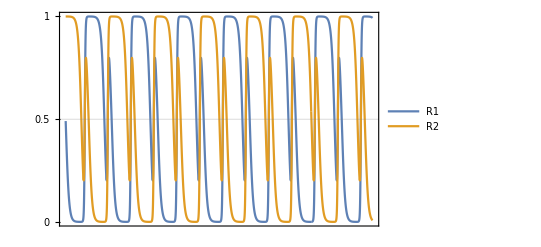

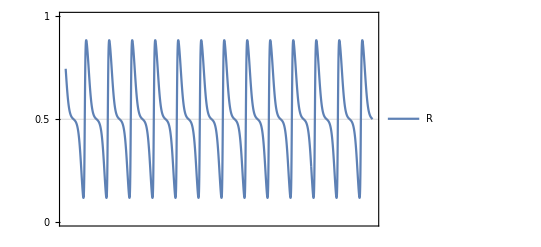

```mathematica
MM=ListLinePlot[{X1,X2},PlotRange->{{0,10000},{0,1}},PlotLegends->{"R1","R2"},Frame->True,FrameStyle->Directive[Black],FrameTicks->{{{0,0.5,1},None},{{190000,195000,200000},None}},GridLines->{None,{0.5}}]
MMM=ListLinePlot[{X},PlotLegends->{"R"},Frame->True,FrameStyle->Directive[Black],FrameTicks->{{{0,0.5,1},None},{{190000,195000,200000},None}},GridLines->{None,{0.5}},PlotRange->{{0,10000},{0,1}}]
```

#### f = 0.22

```mathematica
μ88f022=Table[{0.9*0.9*0.8/2,0.9*0.9*0.2/2,0.9*0.1*0.8/2,0.9*0.1*0.2/2,0.1*0.9*0.8/2,0.1*0.9*0.2/2,0.1*0.1*0.8/2,0.1*0.1*0.2/2,0.9*0.9*0.8/2,0.9*0.9*0.2/2,0.9*0.1*0.8/2,0.9*0.1*0.2/2,0.1*0.9*0.8/2,0.1*0.9*0.2/2,0.1*0.1*0.8/2,0.1*0.1*0.2/2,1},{i,1,200000}];
```

```mathematica
For[i=2,i≤200000,++i,
If[Mod[i,20000]==0,Print[i]];
μ88f022[[i]]=HaplotypesPr[{0.5,0.5},{0.5,0.5,1,0.5,0.22},{10^-8,10^-8,10^-8},μ88f022[[i-1]]]];
```

```mathematica
Export["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ88f022.txt",μ88f022,"Table"];
```

```mathematica
μ88f022=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ88f022.txt","Table"];
```

```mathematica
ListRμ88f022=Table[{i,RMean[μ88f022[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ88f022]}];
ListR1μ88f022=Table[{i,R1Mean[μ88f022[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ88f022]}];
ListR2μ88f022=Table[{i,R2Mean[μ88f022[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ88f022]}];
```

```mathematica
Export["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ88f022_R1.txt",ListR1μ88f022,"Table"];
Export["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ88f022_R2.txt",ListR2μ88f022,"Table"];
Export["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ88f022_R.txt",ListRμ88f022,"Table"];
```

```mathematica
ListRμ88f022=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ88f022_R.txt","Table"];
ListR1μ88f022=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ88f022_R1.txt","Table"];
ListR2μ88f022=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ88f022_R2.txt","Table"];
```

```mathematica
a={{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0},{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0}};
vec2=Table[a.μ88f022[[i*10]],{i,19000,20000}];
vec1=Table[a.μ88f022[[i*10]],{i,1000,2000}];
```

```mathematica
CO1=Array[0*1&,1001];
CO2=Array[0*1&,1001];
For[j=1,j<1002,++j,
CO2[[j]]=ListRμ88f022[[190000+(j-1)*10,2]];
CO1[[j]]=ListRμ88f022[[10000+(j-1)*10,2]]];
```

```mathematica
finter1=Interpolation[#,InterpolationOrder->5,Method->"Spline"]&/@Transpose[vec1];
finter2=Interpolation[#,InterpolationOrder->5,Method->"Spline"]&/@Transpose[vec2];
rinter1=ListInterpolation[CO1];
rinter2=ListInterpolation[CO2];
p1=ParametricPlot3D[Through[finter1[t]],{t,1,Length[vec1]},ColorFunction->Function[{x,y,z,t},ColorData["Rainbow"][rinter1[t]]],ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[Thickness[0.004],Opacity[1]],LabelStyle->Directive[ Black],Ticks->{None}];
p2=ParametricPlot3D[Through[finter2[t]],{t,1,Length[vec2]},ColorFunction->Function[{x,y,z,t},ColorData["Rainbow"][rinter2[t]]],ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[Thickness[0.004],Opacity[1]],LabelStyle->Directive[ Black],Ticks->{None}];
CubePlot=Show[{p1,p2}]
```

-Graphics3D-

```mathematica
p2
```

-Graphics3D-

```mathematica
X1=Table[{0,0},{i,1,10000}];
X2=Table[{0,0},{i,1,10000}];
X=Table[{0,0},{i,1,10000}];
```

```mathematica
For[ii=1,ii≤10000,++ii,
X1[[ii]]={ii,ListR1μ88f022[[190000+ii]][[2]]};
X2[[ii]]={ii,ListR2μ88f022[[190000+ii]][[2]]};
X[[ii]]={ii,ListRμ88f022[[190000+ii]][[2]]};]
```

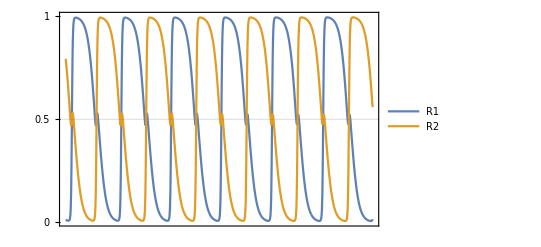

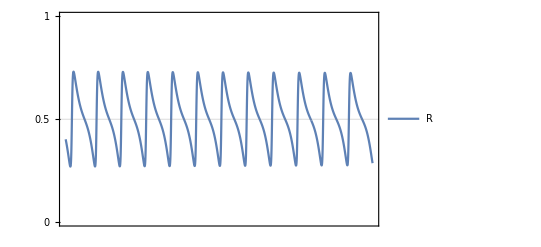

```mathematica
MM=ListLinePlot[{X1,X2},PlotRange->{{0,10000},{0,1}},PlotLegends->{"R1","R2"},Frame->True,FrameStyle->Directive[Black],FrameTicks->{{{0,0.5,1},None},{{190000,195000,200000},None}},GridLines->{None,{0.5}}]
MMM=ListLinePlot[{X},PlotLegends->{"R"},Frame->True,FrameStyle->Directive[Black],FrameTicks->{{{0,0.5,1},None},{{190000,195000,200000},None}},GridLines->{None,{0.5}},PlotRange->{{0,10000},{0,1}}]
```

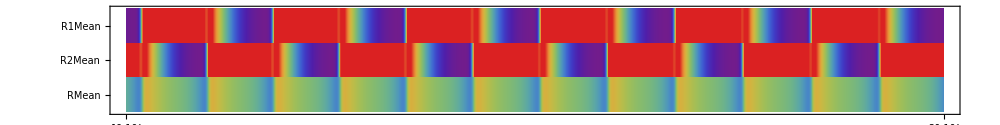

```mathematica
MM=MatrixPlot[{2*ListR1μ88f022[[190000;;200000,2]],2*ListR2μ88f022[[190000;;200000,2]],ListRμ88f022[[190000;;200000,2]]},ColorFunction->ColorData["Rainbow"],ColorFunctionScaling->False,MaxPlotPoints->10000,AspectRatio->1/8,ImageSize->1000,Frame->True,FrameStyle->Thick,FrameTicks->{{{1,"R1Mean"},{2,"R2Mean"},{3,"RMean"}},{{0,"19.10^4"},{10000,"20.10^4"}}},FrameTicksStyle->Directive[Black,Bold,16,Opacity[0],FontOpacity->1],PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LabelStyle->Directive[Bold,12,Black],LegendMarkerSize->150],Right]]
```

### μA = 10^-6

#### f = 0.09

```mathematica
μ68f009=Table[{0.9*0.9*0.8/2,0.9*0.9*0.2/2,0.9*0.1*0.8/2,0.9*0.1*0.2/2,0.1*0.9*0.8/2,0.1*0.9*0.2/2,0.1*0.1*0.8/2,0.1*0.1*0.2/2,0.9*0.9*0.8/2,0.9*0.9*0.2/2,0.9*0.1*0.8/2,0.9*0.1*0.2/2,0.1*0.9*0.8/2,0.1*0.9*0.2/2,0.1*0.1*0.8/2,0.1*0.1*0.2/2,1},{i,1,200000}];
```

```mathematica
For[i=2,i≤200000,++i,
If[Mod[i,20000]==0,Print[i]];
μ68f009[[i]]=HaplotypesPr[{0.5,0.5},{0.5,0.5,1,0.5,0.18},{10^-6,10^-8,10^-8},μ68f009[[i-1]]]];
```

```mathematica
Export["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ68f009.txt",μ68f009,"Table"];
```

```mathematica
μ68f009=Import["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ68f009.txt","Table"];
```

```mathematica
ListRμ68f009=Table[{i,RMean[μ68f009[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ68f009]}];
ListR1μ68f009=Table[{i,R1Mean[μ68f009[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ68f009]}];
ListR2μ68f009=Table[{i,R2Mean[μ68f009[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ68f009]}];
```

```mathematica
Export["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ68f009_R1.txt",ListR1μ68f009,"Table"];
Export["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ68f009_R2.txt",ListR2μ68f009,"Table"];
Export["/Users/fuwork/Dropbox (Royal Holloway)/Research/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ68f009_R.txt",ListRμ68f009,"Table"];
```

```mathematica
ListRμ68f009=Import["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ68f009_R.txt","Table"];
ListR1μ68f009=Import["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ68f009_R1.txt","Table"];
ListR2μ68f009=Import["/Users/ff/Dropbox/Fyon/RecombinationHotspost/Project 1 - Recombination Hotspot Dynamics with Mutation/Two_targets/Data/μ68f009_R2.txt","Table"];
```

```mathematica
a={{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0},{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0}};
vec2=Table[a.μ68f009[[i*10]],{i,19000,20000}];
vec1=Table[a.μ68f009[[i*10]],{i,1000,2000}];
```

```mathematica
CO1=Array[0*1&,1001];
CO2=Array[0*1&,1001];
For[j=1,j<1002,++j,
CO2[[j]]=ListRμ68f009[[190000+(j-1)*10,2]];
CO1[[j]]=ListRμ68f009[[10000+(j-1)*10,2]]];
```

```mathematica
finter1=Interpolation[#,InterpolationOrder->5,Method->"Spline"]&/@Transpose[vec1];
finter2=Interpolation[#,InterpolationOrder->5,Method->"Spline"]&/@Transpose[vec2];
rinter1=ListInterpolation[CO1];
rinter2=ListInterpolation[CO2];
p1=ParametricPlot3D[Through[finter1[t]],{t,1,Length[vec1]},ColorFunction->Function[{x,y,z,t},ColorData["Rainbow"][rinter1[t]]],ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[Thickness[0.004],Opacity[1]],LabelStyle->Directive[ Black],Ticks->{None}];
p2=ParametricPlot3D[Through[finter2[t]],{t,1,Length[vec2]},ColorFunction->Function[{x,y,z,t},ColorData["Rainbow"][rinter2[t]]],ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[Thickness[0.004],Opacity[1]],LabelStyle->Directive[ Black],Ticks->{None}];
CubePlot=Show[{p1,p2}]
```

-Graphics3D-

```mathematica
p2
```

-Graphics3D-

```mathematica
X1=Table[{0,0},{i,1,10000}];
X2=Table[{0,0},{i,1,10000}];
X=Table[{0,0},{i,1,10000}];
```

```mathematica
For[ii=1,ii≤10000,++ii,
X1[[ii]]={ii,ListR1μ68f009[[190000+ii]][[2]]};
X2[[ii]]={ii,ListR2μ68f009[[190000+ii]][[2]]};
X[[ii]]={ii,ListRμ68f009[[190000+ii]][[2]]};]
```

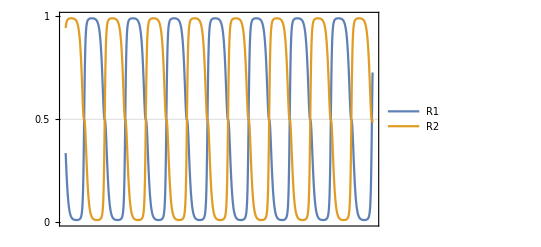

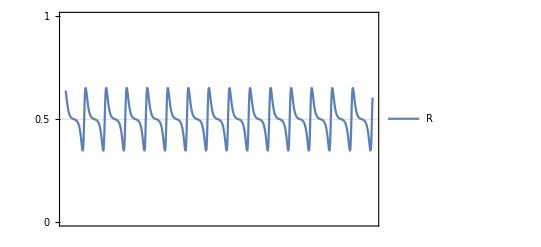

```mathematica
MM=ListLinePlot[{X1,X2},PlotRange->{{0,10000},{0,1}},PlotLegends->{"R1","R2"},Frame->True,FrameStyle->Directive[Black],FrameTicks->{{{0,0.5,1},None},{{190000,195000,200000},None}},GridLines->{None,{0.5}}]
MMM=ListLinePlot[{X},PlotLegends->{"R"},Frame->True,FrameStyle->Directive[Black],FrameTicks->{{{0,0.5,1},None},{{190000,195000,200000},None}},GridLines->{None,{0.5}},PlotRange->{{0,10000},{0,1}}]
```

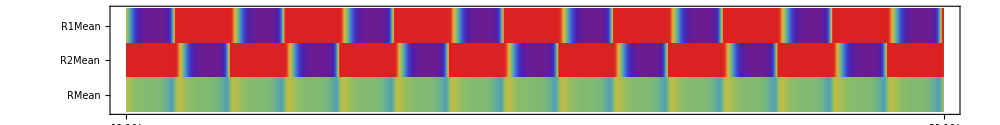

```mathematica
MM=MatrixPlot[{2*ListR1μ68f009[[190000;;200000,2]],2*ListR2μ68f009[[190000;;200000,2]],ListRμ68f009[[190000;;200000,2]]},ColorFunction->ColorData["Rainbow"],ColorFunctionScaling->False,MaxPlotPoints->10000,AspectRatio->1/8,ImageSize->1000,Frame->True,FrameStyle->Thick,FrameTicks->{{{1,"R1Mean"},{2,"R2Mean"},{3,"RMean"}},{{0,"19.10^4"},{10000,"20.10^4"}}},FrameTicksStyle->Directive[Black,Bold,16,Opacity[0],FontOpacity->1],PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LabelStyle->Directive[Bold,12,Black],LegendMarkerSize->150],Right]]
```

#### f = 0.18

See Figure 5

#### f = 0.22

```mathematica
μ68f022=Table[{0.9*0.9*0.8/2,0.9*0.9*0.2/2,0.9*0.1*0.8/2,0.9*0.1*0.2/2,0.1*0.9*0.8/2,0.1*0.9*0.2/2,0.1*0.1*0.8/2,0.1*0.1*0.2/2,0.9*0.9*0.8/2,0.9*0.9*0.2/2,0.9*0.1*0.8/2,0.9*0.1*0.2/2,0.1*0.9*0.8/2,0.1*0.9*0.2/2,0.1*0.1*0.8/2,0.1*0.1*0.2/2,1},{i,1,200000}];
```

```mathematica
For[i=17399,i≤200000,++i,
If[Mod[i,20000]==0,Print[i]];
μ68f022[[i]]=HaplotypesPr[{0.5,0.5},{0.5,0.5,1,0.5,0.22},{10^-6,10^-8,10^-8},μ68f022[[i-1]]]];
```

```mathematica
Export["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ88f022.txt",μ68f022,"Table"];
```

```mathematica
μ88f022=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ88f022.txt","Table"];
```

```mathematica
ListRμ68f022=Table[{i,RMean[μ68f022[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ68f022]}];
ListR1μ68f022=Table[{i,R1Mean[μ68f022[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ68f022]}];
ListR2μ68f022=Table[{i,R2Mean[μ68f022[[i,;;]],{0.5,0.5,1,1}]},{i,1,Length[μ68f022]}];
```

```mathematica
Export["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ68f022_R1.txt",ListR1μ68f022,"Table"];
Export["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ68f022_R2.txt",ListR2μ68f022,"Table"];
Export["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ68f022_R.txt",ListRμ68f022,"Table"];
```

```mathematica
ListRμ68f022=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ68f022_R.txt","Table"];
ListR1μ68f022=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ68f022_R1.txt","Table"];
ListR2μ68f022=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Two_targets\\Data\\μ68f022_R2.txt","Table"];
```

```mathematica
a={{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0},{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0}};
vec2=Table[a.μ68f022[[i*10]],{i,19000,20000}];
vec1=Table[a.μ68f022[[i*10]],{i,1000,2000}];
```

```mathematica
CO1=Array[0*1&,1001];
CO2=Array[0*1&,1001];
For[j=1,j<1002,++j,
CO2[[j]]=ListRμ68f022[[190000+(j-1)*10,2]];
CO1[[j]]=ListRμ68f022[[10000+(j-1)*10,2]]];
```

```mathematica
finter1=Interpolation[#,InterpolationOrder->5,Method->"Spline"]&/@Transpose[vec1];
finter2=Interpolation[#,InterpolationOrder->5,Method->"Spline"]&/@Transpose[vec2];
rinter1=ListInterpolation[CO1];
rinter2=ListInterpolation[CO2];
p1=ParametricPlot3D[Through[finter1[t]],{t,1,Length[vec1]},ColorFunction->Function[{x,y,z,t},ColorData["Rainbow"][rinter1[t]]],ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[Thickness[0.004],Opacity[1]],LabelStyle->Directive[ Black],Ticks->{None}];
p2=ParametricPlot3D[Through[finter2[t]],{t,1,Length[vec2]},ColorFunction->Function[{x,y,z,t},ColorData["Rainbow"][rinter2[t]]],ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[Thickness[0.004],Opacity[1]],LabelStyle->Directive[ Black],Ticks->{None}];
CubePlot=Show[{p1,p2}]
```

-Graphics3D-

```mathematica
p2
```

-Graphics3D-

```mathematica
X1=Table[{0,0},{i,1,10000}];
X2=Table[{0,0},{i,1,10000}];
X=Table[{0,0},{i,1,10000}];
```

```mathematica
For[ii=1,ii≤10000,++ii,
X1[[ii]]={ii,ListR1μ68f022[[190000+ii]][[2]]};
X2[[ii]]={ii,ListR2μ68f022[[190000+ii]][[2]]};
X[[ii]]={ii,ListRμ68f022[[190000+ii]][[2]]};]
```

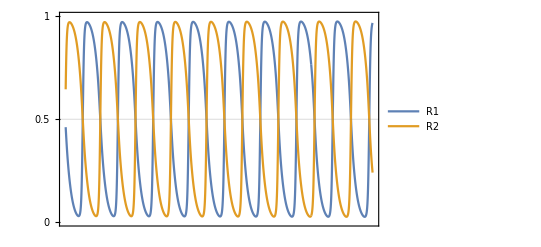

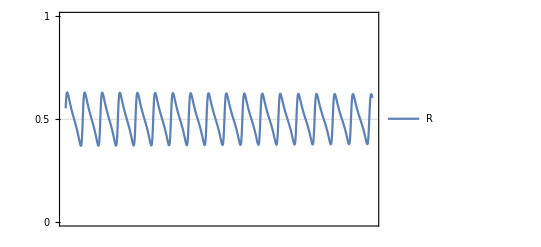

```mathematica
MM=ListLinePlot[{X1,X2},PlotRange->{{0,10000},{0,1}},PlotLegends->{"R1","R2"},Frame->True,FrameStyle->Directive[Black],FrameTicks->{{{0,0.5,1},None},{{190000,195000,200000},None}},GridLines->{None,{0.5}}]
MMM=ListLinePlot[{X},PlotLegends->{"R"},Frame->True,FrameStyle->Directive[Black],FrameTicks->{{{0,0.5,1},None},{{190000,195000,200000},None}},GridLines->{None,{0.5}},PlotRange->{{0,10000},{0,1}}]
```

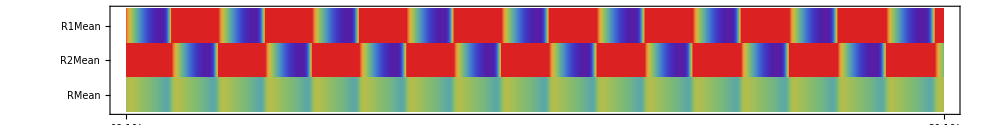

```mathematica
MM=MatrixPlot[{2*ListR1μ68f022[[190000;;200000,2]],2*ListR2μ68f022[[190000;;200000,2]],ListRμ68f022[[190000;;200000,2]]},ColorFunction->ColorData["Rainbow"],ColorFunctionScaling->False,MaxPlotPoints->10000,AspectRatio->1/8,ImageSize->1000,Frame->True,FrameStyle->Thick,FrameTicks->{{{1,"R1Mean"},{2,"R2Mean"},{3,"RMean"}},{{0,"19.10^4"},{10000,"20.10^4"}}},FrameTicksStyle->Directive[Black,Bold,16,Opacity[0],FontOpacity->1],PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LabelStyle->Directive[Bold,12,Black],LegendMarkerSize->150],Right]]
```